# Brainstorming for Systematic Randomness Testing

```mathematica
rule30seq=CellularAutomaton[30, {{1}, 0}, {10000,0}]ᵀ⟦1⟧;
```

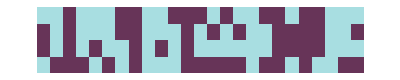

```mathematica
ArrayPlot[Partition[Take[rule30seq,100],25],]
```

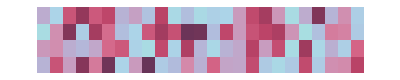

```mathematica
ArrayPlot[Partition[RandomReal[{0,1},100],25],]
```

```mathematica
Autocorrelation
Recurrence quantification analysis
Recurrence plots
AutocorrelationTest
```

http://www-users.math.umn.edu/~garrett/students/reu/pRNGs.pdf

★

https://en.wikipedia.org/wiki/Kolmogorov% E2 %80 %93 Smirnov_test #Kolmogorov % E2 %80 %93 Smirnov_statistic

https://en.wikipedia.org/wiki/Wald% E2 %80 %93 Wolfowitz_runs _test

https://en.wikipedia.org/wiki/Diehard_tests

https://doc.lagout.org/science/0_Computer %20 Science/2_Algorithms/The%20 Art %20 of %20 Computer %20 Programming %20 %28 vol.%202_ %20 Seminumerical %20 Algorithms %29 %20 %283 rd %20 ed.%29%20 %5 BKnuth %201997-11-14%5 D.pdf

An ultimate report

Bin size vs. p-value

## ✓✓ Chi Square Test ★

### Chi Square test for independence — Sequences of 0s and 1s

```mathematica
chiSquareTest01[seq_]:=<|"TestStatistic"->(#2-2#1)^2/#2,"PValue"-> 1.-CDF[ChiSquareDistribution[1],(#2-2#1)^2/#2],"DegreesofFreedom"->1|>&[Total[seq],Length[seq]]
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&]]:=chiSquareTest01[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&],"PValue"]:=chiSquareTest01[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,#==0||#==1&],"TestStatistic"]:=chiSquareTest01[seq]["TestStatistic"];
```

```mathematica
ChiSquareTest[rule30seq]
```

0.515713

### Chi square test for independence — Random reals between 0 and 1

```mathematica
sequence=RandomReal[{0,1},100];
```

```mathematica
N@1-CDF[ChiSquareDistribution[Length[sequence]-2],Total[(BinCounts[sequence,1/Length[sequence]]-1)^2/1]]
```

0.651641

```mathematica
chiSquareTestRandomReal[seq_]:=Module[{stat=Total[(BinCounts[seq,1/Length[seq]]-1)^2]},
<|"TestStatistic"->stat,"PValue"->1.-CDF[ChiSquareDistribution[Length[seq]-2],stat],"DegreesofFreedom"->Length[seq]-2|>
];
ChiSquareTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&]]:=chiSquareTestRandomReal[seq]["PValue"];
ChiSquareTest[seq_List/;VectorQ[seq,IntervalMemberQ[Interval[{0,1}],#]&&NumberQ[#]&],req_String/;MemberQ[{"TestStatistic","PValue"},req]]:=chiSquareTestRandomReal[seq][req];
```

### Chi square test for independence —Arbitrary distribution

```mathematica
variates=RandomVariate[NormalDistribution[],100];
```

```mathematica
chiSquareTestRandomReal[CDF[NormalDistribution[],variates]]
```

<|TestStatistic→94,PValue→0.595568|>

```mathematica
chiSquareTestArbitraryDistribution[seq_,dist_]:=chiSquareTestRandomReal[CDF[dist,seq]]
```

```mathematica
chiSquareTestArbitraryDistribution[RandomVariate[ChiSquareDistribution[100],1000],ChiSquareDistribution[100]]
```

<|TestStatistic→950,PValue→0.859289,DegreesofFreedom→998|>

## ✓✓ Kolmogorov-Smirnov Test

```mathematica
sequence=RandomReal[{0,1},100];
```

The Kolmogorov-Smirnov Test is already implemented in the Wolfram Language

```mathematica
KolmogorovSmirnovTest[sequence,UniformDistribution[],"PValue"]
```

0.955143

## ✓ Serial Test — sequences of length two ✶

Only works for 0s and 1s!

### Brainstorming

```mathematica
sequence=RandomInteger[{0,1},100]
```

{0,0,1,1,0,0,1,1,1,0,0,0,0,0,0,1,0,0,0,1,0,1,0,0,1,1,0,1,1,1,1,1,1,0,1,1,0,1,0,1,1,1,0,1,0,0,1,1,1,1,1,0,0,0,1,0,0,1,1,1,1,1,0,0,1,0,1,1,0,1,0,1,1,1,0,1,1,1,1,1,0,0,0,1,0,1,1,1,1,0,1,0,1,0,1,0,0,1,1,1}

```mathematica
sequence//Row
```

0011001110000001000101001101111110110101110100111110001001111100101101011101111100010111101010100111

```mathematica
Count[sequence,Sequence[0,1]]
```

5

```mathematica
Count[sequence,#/.List->Sequence]&/@Tuples[{0,1},2]
```

{0,5,0,5}

```mathematica
Replace[Tuples[{0,1},2],List->Sequence,2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Tuples[{0,1},2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]
```

{1,3,4,1}

```mathematica
cts
```

DataDistribution[…]

```mathematica
cts=Table[SequenceCount[RandomInteger[{0,1},100],#]&/@Tuples[{0,1},2],100000]
```

{{12,24,25,13},{19,24,29,15},{13,27,28,19},{15,24,27,11},{17,19,22,17},{19,19,22,23},{19,28,18,15},{16,19,27,14},{13,26,21,16},{9,28,27,13},99980,{14,24,28,16},{17,30,27,20},{16,23,22,18},{8,28,22,15},{19,26,27,15},{10,25,27,20},{18,21,25,19},{16,26,29,21},{15,28,26,18},{12,21,24,17}}
 |  |  |  |

```mathematica
$mcts=N@Mean[cts]
```

{16.5541,24.7637,24.7327,16.5385}

```mathematica
ClearAll[statdist]
```

```mathematica
statdist[num_]:=Module[{n=num,cts=Table[SequenceCount[RandomInteger[{0,1},num],#]&/@Tuples[{0,1},2],100000],mcts},
mcts=N@Mean[cts];
Total[(#-mcts)^2/mcts]&/@N@cts
]
```

```mathematica
statdist[10]
```

{0.66598,4.70229,1.70427,1.33555,1.8321,3.37313,0.66598,99986,0.605268,1.79685,2.88841,0.382571,3.34872,1.04893,3.4083}
 |  |  |  |

```mathematica
df[dist_]:=ν/.FindDistributionParameters[dist,ChiSquareDistribution[ν]]
```

```mathematica
df[statdist[10]]
```

2.35238

```mathematica
Table[df[statdist[n]],{n,100,5000,500}]
```

{2.16794,2.18437,2.16289,2.15685,2.17999,2.17457,2.16051,2.16972,2.17108,2.15506}

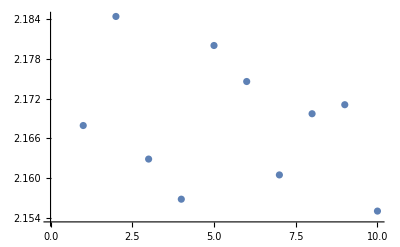

```mathematica
ListPlot[%]
```

```mathematica
ν=df[statdist[1000]]
```

2.18316

★ Test statistic has the form

stat = (freq_(0,0)-n µ_(freq. 0,0))^2/(n µ_(freq. 0,0))+(freq_(0,1)-n µ_(freq. 0,1))^2/(n µ_(freq. 0,1))+(freq_(1,1)-n µ_(freq. 1,1))^2/(n µ_(freq. 1,1))+(freq_(1,0)-n µ_(freq. 1,0))^2/(n µ_(freq. 1,0))
¬stat \[Distributed] χ^2(ν  ≈ 1.90)
stat\[Distributed] GammaDistribution(α,β)

Distribution of test statistic is chi square — for high lengths of (n ≥ 100) sequences ★ CONSTANT ν ★

```mathematica
mcts
```

{16.5541,24.7637,24.7327,16.5385}

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]-$mcts
```

{13,25,24,19}

Mean counts ratio does not vary with sequence length above a certain length

```mathematica
mcts[n_]:=Mean[Table[N@SequenceCount[RandomInteger[{0,1},n],#]&/@Tuples[{0,1},2],10000]]
```

```mathematica
Table[mcts[n]/n,{n,100,5000,500}]
```

{{0.16553,0.2474,0.24766,0.1661},{0.16612,0.249135,0.24996,0.166392},{0.166419,0.249994,0.249593,0.166629},{0.166518,0.249887,0.249653,0.166768},{0.16661,0.249879,0.24989,0.166915},{0.166819,0.249865,0.249909,0.166517},{0.166449,0.249847,0.249868,0.166547},{0.166895,0.250046,0.250115,0.166822},{0.16656,0.249657,0.250096,0.166809},{0.166622,0.250003,0.24997,0.166721}}

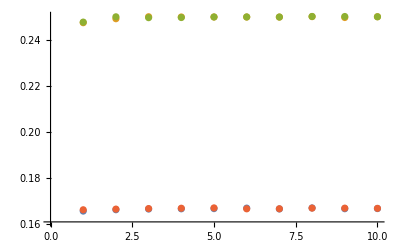

```mathematica
ListPlot[%ᵀ]
```

```mathematica
$mctsrat=mcts[1000]/1000
```

{0.166585,0.249666,0.249679,0.166447}

```mathematica
seqStat[seq_]:=Total[((SequenceCount[seq,#]&/@Tuples[{0,1},2])-Length[seq]$mctsrat)^2/(Length[seq]$mctsrat)]
```

```mathematica
seqStat/@RandomInteger[{0,1},{10^5,1000}];
```

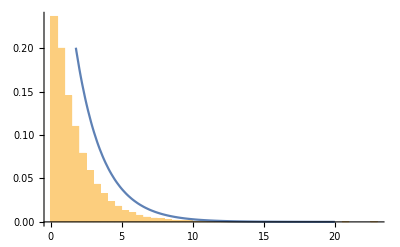

```mathematica
Show[Histogram[%773,Automatic,"Probability",PlotRange->All],Plot[PDF[ChiSquareDistribution[1.9061033494727069],x],{x,0,20}]]
```

```mathematica
FindDistributionParameters[%794,ChiSquareDistribution[n]]
```

{n→1.9061}

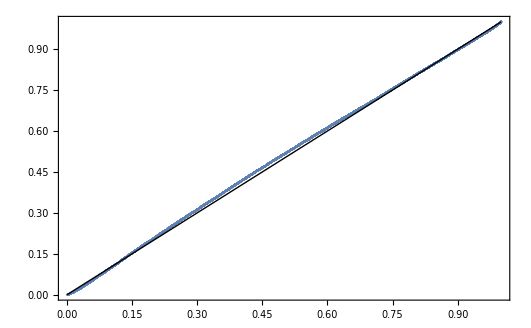

```mathematica
ProbabilityPlot[%794,%812]
```

```mathematica
df[n_]:=degreesOfFreedom/.FindDistributionParameters[seqStat/@RandomInteger[{0,1},{10^5,n}],ChiSquareDistribution[degreesOfFreedom]]
```

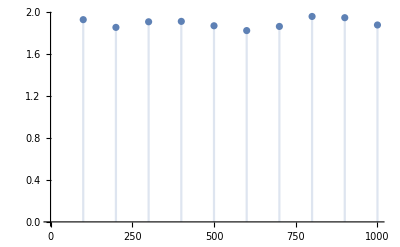

```mathematica
DiscretePlot[df[n],{n,100,1000,100}]
```

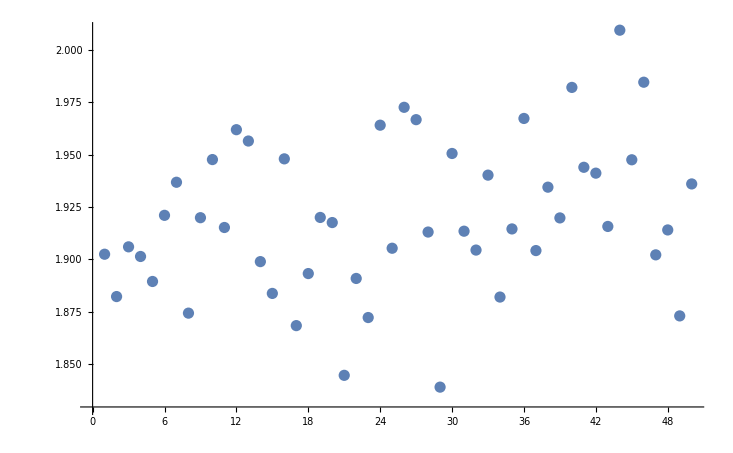

```mathematica
ListPlot[%611]
```

```mathematica
Table[df[n],{n,100,5000,100}];
```

```mathematica
df[1000]
```

1.91098

```mathematica
Tuples[{0,1},2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
Table[1-CDF[ChiSquareDistribution[1.91],seqStat[RandomInteger[{0,1},1000]]],10000];
```

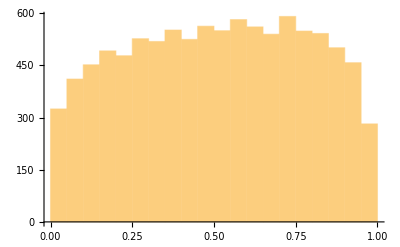

```mathematica
Histogram[%]
```

```mathematica
DistributionFitTest[%750,UniformDistribution[]]
```

0.

Run experiments to show that distribution of stat converges to something else—GammaDistribution?

In paper, note and discuss invariance under list length

```mathematica
FindDistribution[%794,TargetFunctions->{GammaDistribution}]
```

GammaDistribution[1.12244,1.53418]

```mathematica
GammaDistribution
```

```mathematica
Manipulate[Show[Histogram[%794,Automatic,"Probability"],Plot[PDF[%812,x],{x,0,8}]],{ν,0,2}]
```

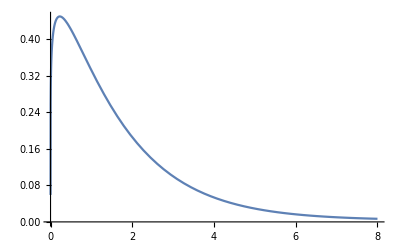

```mathematica
Plot[PDF[%801,x],{x,0,8}]
```

### Procedure & Methods — Outline

Generate a sequence

```mathematica
sequence=RandomInteger[{0,1},100];
sequence//Row
```

1010001010010101011011110011001111011100101110110001100101101011101010011110100011101011001001010010

Format is {{0,0},{0,1},{1,0},{1,1}} for frequency of a sequence.

```mathematica
SequenceCount[sequence,#]&/@Tuples[{0,1},2]
```

{12,30,31,16}

Find a statistic that measures the deviation from expected frequency

stat = (freq_(0,0)-n µ_(freq. 0,0))^2/(n µ_(freq. 0,0))+(freq_(0,1)-n µ_(freq. 0,1))^2/(n µ_(freq. 0,1))+(freq_(1,1)-n µ_(freq. 1,1))^2/(n µ_(freq. 1,1))+(freq_(1,0)-n µ_(freq. 1,0))^2/(n µ_(freq. 1,0))

Find the mean counts empirically for a given list length n

```mathematica
mcts[n_,samplesize_]:=Mean[Table[N@SequenceCount[RandomInteger[{0,1},n],#]&/@Tuples[{0,1},2],samplesize]]
```

How do these mean counts behave?

```mathematica
Compile[mcts]
```

Compile::argtu: Compile called with 1 argument; 2 or 3 arguments are expected.

Compile[mcts]

```mathematica
ParallelTable[mcts[n,10000]/n,{n,100,1000,100}]
```

{{0.166138,0.247454,0.247369,0.165673},{0.166174,0.248824,0.248729,0.166274},{0.166295,0.248908,0.249039,0.166312},{0.166499,0.249255,0.249211,0.166439},{0.166484,0.249509,0.24975,0.166638},{0.166575,0.249584,0.249569,0.166569},{0.166559,0.249529,0.249706,0.16649},{0.166497,0.249854,0.249716,0.166422},{0.166478,0.249666,0.24974,0.166456},{0.166533,0.249579,0.249745,0.166798}}

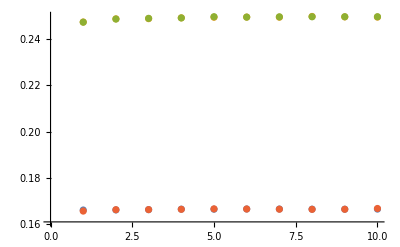

```mathematica
ListPlot[%ᵀ]
```

Ratios between the mean counts and the list length is independent of list length for high (n > 100) list lengths. We can calculate the mean ratios

```mathematica
Compile[{{x,_Real}},mcts[500,x]]
```

CompiledFunction[…]

```mathematica
$mctsrat=Parallelize[(%226[100000])/500]
```

Parallelize::nopar1: (%226[100000])/500 cannot be parallelized; proceeding with sequential evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 1; proceeding with uncompiled evaluation.

{0.166439,0.2495,0.249533,0.166391}

```mathematica
$mctsrat=mcts[500,100000]/500
```

{0.166392,0.249491,0.249536,0.166482}

Generating the statistic is then easy

```mathematica
seqStat[seq_]:=Total[((SequenceCount[seq,#]&/@Tuples[{0,1},2])-Length[seq]$mctsrat)^2/(Length[seq]$mctsrat)]
```

```mathematica
seqStat[sequence]
```

3.81022

How does this statistic behave?

```mathematica
dist[n_,samplesize_]:=ParallelTable[seqStat[RandomInteger[{0,1},n]],samplesize]
```

```mathematica
distsample500=dist[500,100000];
```

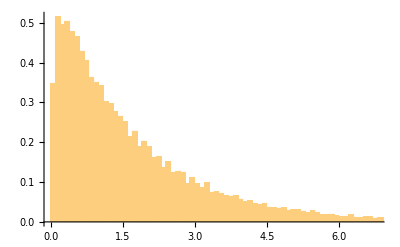

```mathematica
Histogram[distsample500,{.1},"PDF"]
```

This distribution resembles the gamma distribution.

```mathematica
fitdist500=GammaDistribution[α,β]/.FindDistributionParameters[distsample500,GammaDistribution[α,β]]
```

GammaDistribution[1.12973,1.52119]

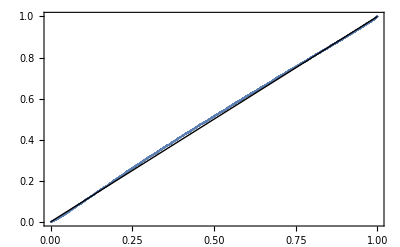

```mathematica
ProbabilityPlot[distsample500,fitdist500]
```

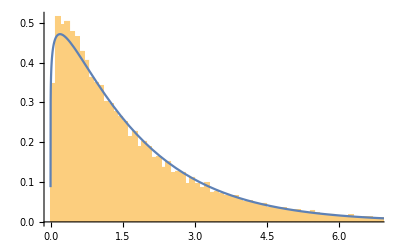

```mathematica
Show[Histogram[distsample500,300,"PDF"],Plot[PDF[fitdist500,x],{x,0,8}]]
```

We can see from the probability plot that this is a very strong fit! We can see that the p-value is low, but not tiny!

```mathematica
DistributionFitTest[distsample500,fitdist500]
```

0.00227318

How do the shape parameters behave with different sequence lengths

```mathematica
αβparams[n_,samplesize_]:=FindDistributionParameters[dist[n,samplesize],GammaDistribution[α,β]]
```

```mathematica
paramvslength=Table[{α,β}/.αβparams[n,10000],{n,100,10000,1000}];
```

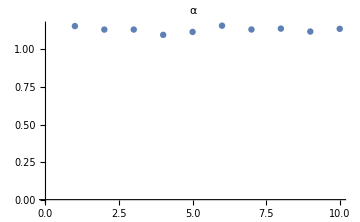
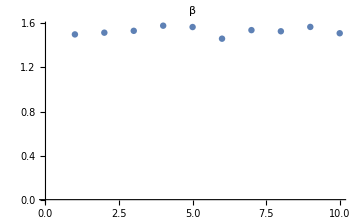

```mathematica
Row@{ListPlot[paramvslengthᵀ⟦1⟧,],ListPlot[paramvslengthᵀ⟦2⟧,]}
```

We can see that the parameters hardly vary and do not vary consistently with list length. We can then find parameters we like.

```mathematica
$params=αβparams[1000,10000]
```

{α→1.12921,β→1.56052}

```mathematica
$fitdist=GammaDistribution[α,β]/.$params
```

GammaDistribution[1.12921,1.56052]

We can now generate p-values

```mathematica
1-CDF[$fitdist,seqStat[sequence]]
```

General::munfl: Exp[-55198.6] is too small to represent as a normalized machine number; precision may be lost.

0.

```mathematica
sequence={1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,1,0,0,1}
```

{1,0,0,1,0,1,0,1,0,0,0,1,1,0,0,1,0,0,1}

```mathematica
1-CDF[$fitdist,seqStat[sequence]]
```

0.261012

```mathematica
1-CDF[$fitdist,seqStat[#]]&/@RandomInteger[{0,1},{100000,100}];
```

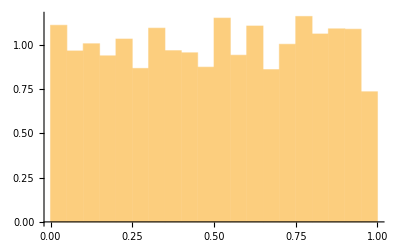

```mathematica
Histogram[%,Automatic,"PDF"]
```

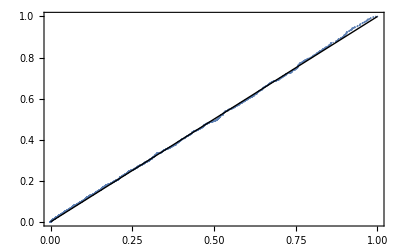

```mathematica
ProbabilityPlot[%977,UniformDistribution[]]
```

We can see that this method is a strong method

```mathematica
1-CDF[$fitdist,seqStat[rule30seq]]
```

0.686934

## ✓ Runs test

### Brainstorming 1

How long are runs?

```mathematica
sequence=RandomReal[{0,1},100000];
```

p67

```mathematica
runlengths=Length/@Split[RandomReal[{0,1},10000],#1<#2&];
```

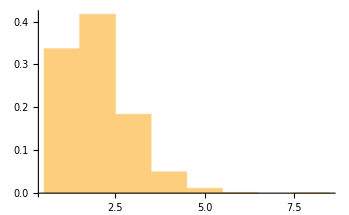

```mathematica
Histogram[%,Automatic,"PDF"]
```

```mathematica
CountsBy[Split[RandomInteger[{0,1},1000]],#⟦1⟧&]
```

<|0→241,1→241|>

```mathematica
runsup[seq_]:=Split[seq,#1<#2&]
```

```mathematica
countRunLength[runsup]
```

<|1→16601,4→2691,2→20833,5→575,3→9118,6→103,7→14,8→3|>

```mathematica
countRunLength[seq_]:=Counts[Length/@Split[seq,#1<#2&]]
```

```mathematica
lengthDist[seq_]:=Length/@Split[seq,#1<#2&]
```

```mathematica
KeyValueMap[#1 #2&,countRunLength[RandomReal[{0,1},1000]]]
```

{384,191,76,306,25,18}

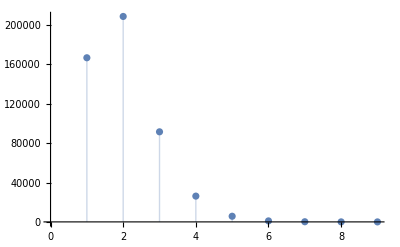

```mathematica
ListPlot[countRunLength[RandomReal[{0,1},1000000]],Filling->Axis]
```

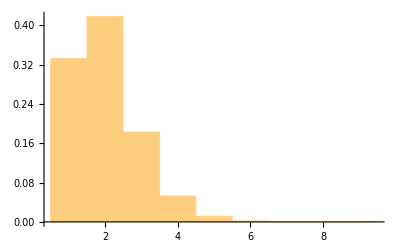

```mathematica
Histogram[lengthDist[RandomReal[{0,1},1000000]],{1},"PDF"]
```

```mathematica
Manipulate[Histogram[lengthDist[Take[sequence,n]],{1},"PDF",PlotRange->{{0,10},{0,1}},PlotLabel->"n = "<>ToString[n]],{n,1,10000,1}]
```

General::stop: Further output of Histogram::ldata will be suppressed during this calculation.

```mathematica
runLengthRatios=Counts[lengthDist[RandomReal[{0,1},1000000]]]/1000000.
```

<|1→0.16625,4→0.026537,2→0.20892,3→0.09128,5→0.00569,6→0.001046,7→0.000142,8→0.000023,9→2.×10^-6|>

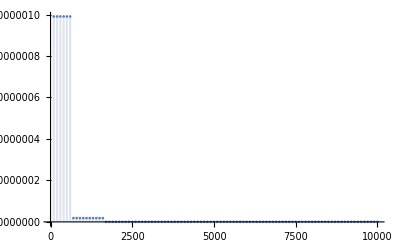

```mathematica
DiscretePlot[Total[Values[KeySort[Append[#1,AssociationThread[Complement[Keys[#1],Keys[#2]]->ConstantArray[0,Length[Complement[Keys[#1],Keys[#2]]]]]]&[runLenthRatios,Counts[lengthDist[Take[#,n]]]/n]-runLenthRatios]]^2],{n,100,10000,100},PlotRange->All]&[RandomReal[{0,1},10000]]
```

Squares difference form 1 million sample distribution length bin counts  vs sample size to constant distribution

```mathematica
meanRunLengths=ParallelMazp[ N@Mean[Length/@runsup[#]]&,RandomReal[{0,1},{1000,50000}]];
```

```mathematica
meanRunLengthvsSequenceLength=Table[{n, N@Mean[Length/@runsup[RandomReal[{0,1},n]]]},{n,100,10000,500}]
```

{{100,2.04082},{600,1.94805},{1100,1.97842},{1600,2.01005},{2100,1.98675},{2600,2.01238},{3100,1.97452},{3600,2.03275},{4100,2.01672},{4600,2.00786},{5100,2.00236},{5600,1.98371},{6100,2.02658},{6600,1.97723},{7100,2.01361},{7600,1.99737},{8100,1.99507},{8600,1.99629},{9100,1.99868},{9600,2.01174}}

```mathematica
runLengthDistvsSequenceLength=Table[{n, N@Identity[Length/@runsup[RandomReal[{0,1},n]]]},{n,100,10000,500}]
```

{{100,{1.,1.,3.,1.,2.,3.,2.,1.,4.,2.,3.,3.,1.,2.,3.,2.,2.,3.,1.,1.,1.,3.,3.,1.,2.,2.,1.,1.,3.,2.,3.,3.,3.,1.,2.,1.,2.,1.,2.,3.,3.,3.,4.,1.,2.,1.,1.,3.,1.}},18,{9600,{2.,2.,2.,1.,2.,1.,1.,4750,2.,3.,2.,2.,2.,1.,1.}}}
 |  |  |  |

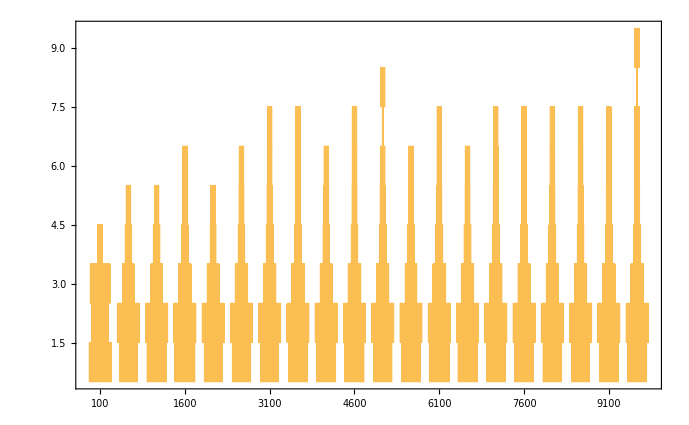

```mathematica
DistributionChart[runLengthDistvsSequenceLengthᵀ⟦2⟧,ChartElementFunction->"HistogramDensity",ChartLabels->runLengthDistvsSequenceLengthᵀ⟦1⟧,PlotRange->{0,All}]
```

Figure above: Runs up lengths vs. sequence length

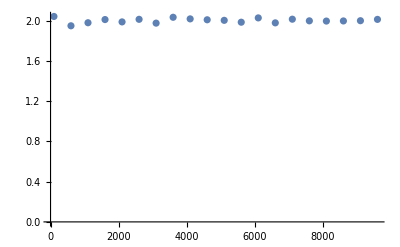

```mathematica
ListPlot[meanRunLengthvsSequenceLength,PlotRange->{0,All}]
```

Figure above: Runs up mean lengths do not vary with sample size

```mathematica
LinearModelFit[meanRunLengthvsSequenceLength,x,x]["RSquared"]
```

0.0644988

```mathematica
$meanRunLengths=N@Mean[Length/@runsup[RandomReal[{0,1},100000]]]
```

1.99617

```mathematica
stat[seq_]:=Total[(seq-$meanRunLengths)^2/($meanRunLengths)]
```

```mathematica
statdist[sequenceLength_,n_]:=stat[#]&/@RandomReal[{0,1},{n,sequenceLength}]
```

```mathematica
Manipulate[ProbabilityPlot[statdist[seqleng,1000]],{seqleng,100,10000,1}]
```

ProbabilityPlot::ldata: statdist[8512,1000] is not a valid dataset, distribution, or a valid list of datasets and distributions.

Figure above: The statistic strongly follows a normal distribution

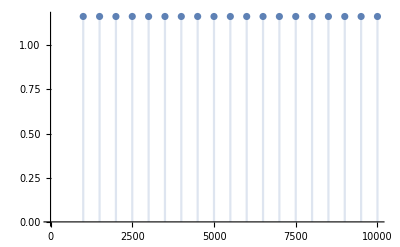

```mathematica
DiscretePlot[μ/seqleng/.FindDistributionParameters[statdist[seqleng,10000],NormalDistribution[μ,σ]],{seqleng,1000,10000,500}]
```

The mean of the distribution varies linearly with the sequence length.

```mathematica
statdistμ[seqleng_]=seqleng μ/10000/.FindDistributionParameters[statdist[10000,10000],NormalDistribution[μ,σ]]
```

1.16129 seqleng

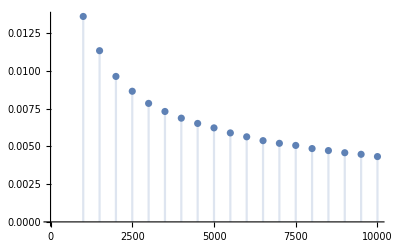

```mathematica
DiscretePlot[σ/seqleng/.FindDistributionParameters[statdist[seqleng,10000],NormalDistribution[μ,σ]],{seqleng,1000,10000,500}]
```

```mathematica
standarddevratvsseqleng=Table[{seqleng,σ/seqleng}/.FindDistributionParameters[statdist[seqleng,10000],NormalDistribution[μ,σ]],{seqleng,1000,10000,500}];
```

```mathematica
nlm=NonlinearModelFit[standarddevratvsseqleng,a x^b,{a,b},x]
```

FittedModel[0.4208/x^0.496322]

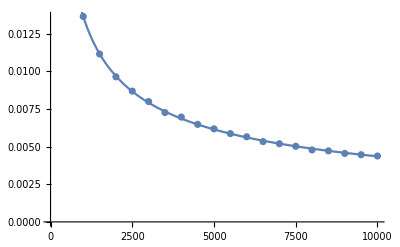

```mathematica
Show[ListPlot[standarddevratvsseqleng],Plot[nlm[seqleng],{seqleng,0,10000}]]
```

σ/seqleng≈nlm[seqleng]
σ≈sqeleng nlm[seqleng]

```mathematica
seqleng nlm[seqleng]
```

0.4208 seqleng^0.503678

```mathematica
statdistσ[seqleng_]=0.4208000593890539 seqleng^0.503677726169205
```

0.4208 seqleng^0.503678

stat \[Distributed] NormalDistribution[statdistμ[seqleng],statdistσ[seqleng]]

```mathematica
stdev[100000]
```

138.824

```mathematica
stat[sequence]
```

116215.

```mathematica
CDF[NormalDistribution[statdistμ[2000],statdistσ[2000]],stat[sequence]]
```

0.

```mathematica
Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[statdistμ[2000],statdistσ[2000]],stat[RandomReal[{0,1},2000]]]
```

0.248275

Test the rate of type 1 error — success!

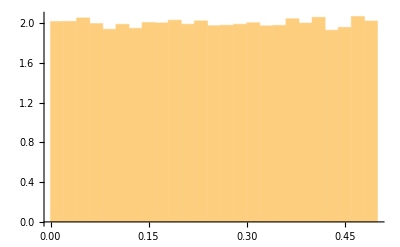

```mathematica
Histogram[Table[Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[statdistμ[2000],statdistσ[2000]],stat[RandomReal[{0,1},2000]]],100000],Automatic,"PDF"]
```

```mathematica
Min[{1-CDF[##],CDF[##]}]&[NormalDistribution[statdistμ[2000],statdistσ[2000]],stat[RandomReal[{0,1},2000]]]
```

0.244446

### Implementing 1

### Brainstorming 2

How many runs do we expect a sequence to have?

```mathematica
binomialFit[samp_]:=FindDistributionParameters[samp,BinomialDistribution[n,p]]
```

```mathematica
binommodelvar1 =Table[binomialFit[Length[Split[#,(#1<#2&)]]&/@RandomReal[{0,1},{1000,nn}]],{nn,1000,10000,1000}]
```

{{n→597,p→0.838211},{n→1208,p→0.828469},{n→1815,p→0.826514},{n→2404,p→0.832156},{n→3010,p→0.830896},{n→3591,p→0.835859},{n→4198,p→0.833928},{n→4793,p→0.834603},{n→5410,p→0.832169},{n→6001,p→0.833213}}

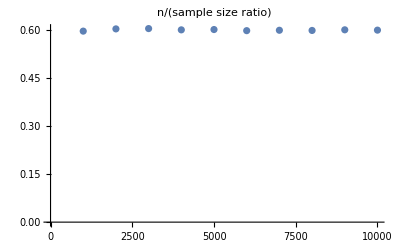

```mathematica
ListPlot[{Table[nn,{nn,1000,10000,1000}],(n/.#&/@binommodelvar1)/Table[nn,{nn,1000,10000,1000}]}ᵀ,]
```

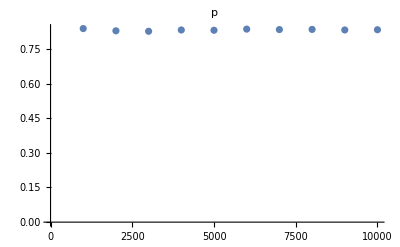

```mathematica
ListPlot[{Table[nn,{nn,1000,10000,1000}],p/.#&/@binommodelvar1}ᵀ,]
```

```mathematica
Mean[N@p/.#&/@binommodelvar1]
```

0.832602

```mathematica
Mean[N@n/.#&/@binommodelvar1]
```

0.832602

```mathematica
BinomialDistribution[0.6007550396825396 n,0.8326016102887464]
```

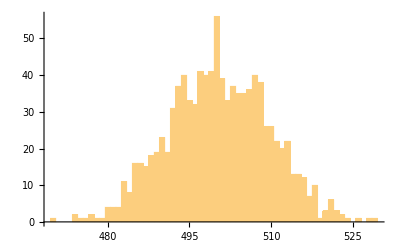

```mathematica
Histogram[%758,100]
```

```mathematica
Length[%758]
```

1000

```mathematica
FindDistributionParameters[%758,BinomialDistribution[n,p]]
```

{n→603,p→0.829773}

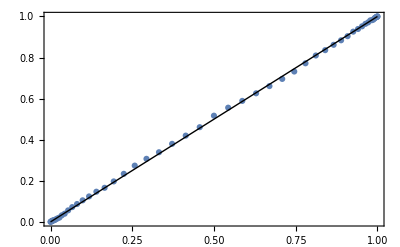

```mathematica
ProbabilityPlot[%758,BinomialDistribution[Round@(0.6007550396825396 1000),0.8326016102887464]]
```

```mathematica
numberOfRunsStat=Length[Split[#,(#1<#2&)]]&
```

Length[Split[#1,#1<#2&]]&

```mathematica
numberOfRunsDistribution[seqleng_]:=BinomialDistribution[Round@(0.6007550396825396  seqleng),0.8326016102887464]
```

```mathematica
numberOfRunsStat/@RandomReal[{0,1},{10000,10000}]
```

{5031,4995,4972,4992,5016,4982,4987,5022,4961,4968,5022,4979,5008,5017,4995,5001,4988,4974,4992,5013,4985,4999,5001,5010,4991,4969,5012,5032,4999,5007,4989,4962,4988,5046,5041,4948,5024,5012,5013,5012,4980,4969,4995,5037,4993,5010,4988,5032,4988,5025,4993,5061,4966,5013,5015,5024,5057,4988,5018,4990,4955,4978,4953,5028,4967,4974,4958,4968,5017,5052,5005,4985,4995,4976,5004,4970,4990,5005,5024,5004,4988,4991,5013,4991,5014,4980,4996,4979,4991,5026,5047,5001,5003,5000,4998,5016,5053,5013,4991,4979,4980,4977,5030,4969,4989,4975,4958,5015,4995,5003,4977,4984,4969,5004,4974,5054,5012,4989,5041,5018,4991,4989,5020,4986,4995,4996,4970,4994,5052,4998,4966,4971,5019,5011,5033,5005,4978,4979,4997,5039,4999,5002,4979,4919,4991,4967,5000,4990,5000,5023,4972,5031,4997,4922,4981,4980,4988,5004,5007,4995,4972,4966,4974,5008,4986,5003,4993,5011,5028,4936,4994,4972,4979,4964,5020,4996,4997,5035,4991,5037,5000,5021,5054,4985,4966,4995,4939,5018,4997,5024,4969,4979,5007,5004,4948,5015,5045,5019,5034,5012,4995,4972,5016,4979,4975,5037,5032,4935,5045,5035,5044,5006,4976,5015,5011,5005,5019,4961,4990,5005,5010,5043,5011,4968,5016,5060,5001,5036,5023,5052,4971,4976,4995,4973,4972,4971,5021,5004,4993,5006,5026,4979,4970,5022,4989,5035,4976,5003,5040,5065,4967,5030,5040,5021,4987,5015,5003,4959,5028,5005,5057,5003,4998,4976,4973,5014,5012,4939,5061,5011,4995,4988,4994,4995,5017,5026,4968,4960,4952,5016,4977,5033,5021,4987,5041,5034,5015,5073,5023,4978,5017,4973,4999,5026,4985,5012,5003,5052,4997,4967,5004,4989,5018,4986,4984,5022,4956,4968,4973,5022,4969,4988,5037,4995,5029,4932,5016,4990,5054,4991,4968,4978,5006,4983,4987,5031,4987,4957,4981,5008,5025,5038,5009,5008,4990,4994,4992,5004,5002,4988,4981,5010,5004,4982,4976,5038,5011,4999,5036,4976,5012,4991,5020,5018,4978,5012,5021,5008,5024,5009,5026,5028,5035,4986,5023,4945,5033,5035,5004,4993,4991,4994,5010,5013,5077,5004,5003,4992,5022,4958,5026,4999,4996,4974,5030,5015,4994,5030,5088,5024,5014,5003,4898,5022,5003,4985,4988,4995,5014,4960,4981,4974,5057,4988,5043,5034,5023,4949,5002,5027,4944,5062,5007,4923,4968,4968,5014,5034,5005,5026,5035,5002,5004,4971,5000,5007,4971,4967,5033,4944,5003,4998,5028,5023,5008,5043,5062,5000,5001,4953,5027,4981,4979,4984,4980,5008,4992,4976,5003,4957,4992,5038,5047,4990,5003,5012,5023,4973,5048,5018,5001,4984,5040,5019,4992,5026,5002,4958,5020,5048,5037,5019,4977,4998,5053,5035,5001,5035,4991,4966,5041,5008,4974,5015,4919,5011,4969,5003,4980,4960,5012,4977,4976,4998,5055,5024,5002,5005,4965,5000,5009,4997,4988,5007,5000,4986,4994,4965,4994,5044,5032,4996,4967,5010,5005,4937,5046,4981,4991,4994,4992,4983,4995,4998,4990,5016,4966,5031,5017,5018,5024,4990,4998,4999,5007,5004,4986,4979,5005,5057,5025,4989,5006,4986,5010,5011,4995,5005,4988,4979,4993,4970,4958,5001,4990,4983,4979,5043,5004,4987,5018,4991,5037,5020,4954,4996,5009,5043,5041,5003,4990,4979,4991,4976,4987,4941,5007,4999,5021,5009,5004,4993,5014,4955,4994,5007,4940,4992,4986,4980,4973,5022,5016,5017,5033,4984,4980,5040,5001,4938,5000,5036,4980,4975,4981,4984,4966,4986,4975,4995,4998,4981,5024,4975,5053,5005,5015,4976,5018,4966,4975,5053,5015,4978,5006,5006,5020,4991,4979,4986,5013,4953,5026,5017,4992,5013,5035,5052,5027,5011,4982,5030,4999,4997,4997,5080,5001,4960,4978,4965,5000,4995,5040,5013,5040,4983,4980,4968,5003,4998,4984,5007,4980,5030,4974,4994,5002,4995,4969,4950,5002,4986,5018,4971,5007,5054,5021,5006,4998,4965,4975,5025,5016,5013,4978,4988,5029,4992,5095,4993,5062,4987,4960,4993,5053,4969,4974,5043,5004,5006,4984,4998,5046,4971,5050,4984,4970,4992,4966,4980,5071,5034,4994,4986,5013,4994,4981,4968,4974,4976,4997,5003,4995,4988,4984,5017,5022,5004,4992,4975,5038,4988,5011,5027,5007,5001,4985,5015,4988,4942,4968,4978,4957,5021,5029,4962,4957,4952,5019,5004,5035,5041,4983,4979,4988,4964,5017,4985,4993,4946,4964,4968,5005,5081,5004,4994,5006,5025,4976,5015,4955,4997,4948,5000,5034,5013,4987,5025,5029,4965,5034,5023,5001,4963,4904,4997,4969,5024,4997,5033,5026,5023,5004,5001,5014,5027,5012,4990,4994,4957,4967,5056,5023,4961,5005,4982,5025,5024,4963,5056,4997,5070,4976,5027,4990,5002,5008,4974,4944,4995,4980,4984,5050,5020,4985,4979,4993,5019,5003,5007,5035,4992,5023,5029,4986,5015,5026,5038,4986,5004,5009,4977,4982,4957,5041,4938,4998,5020,4985,4979,5037,5007,4971,5022,5050,4993,5011,4983,5034,5015,5046,5010,5048,5005,4998,5001,4976,5014,4958,5045,4988,4982,5015,5021,5011,5007,4982,4975,5017,5046,5001,4994,5042,5001,5016,5062,4974,4976,5011,5066,5025,4969,4963,4991,5005,4993,5028,4995,4999,4985,5033,5022,5031,4991,5042,5023,5049,4997,4950,5038,4990,4984,4961,5008,4971,4993,4984,4965,5048,4966,5018,5013,4934,4992,5009,5022,4988,4958,5044,4982,4993,5009,5035,4933,5042,4984,4994,4972,5018,5043,5006,5040,4958,4994,4992,5038,5019,5008,5017,5028,5005,4989,4990,4969,5021,5013,5009,5008,5012,5010,5033,5005,5025,5047,5034,4983,5016,5021,4986,5001,5007,5001,4973,4942,4992,5009,5017,4981,4980,5003,5016,5004,4965,5022,5032,4980,5016,5021,5026,5033,4988,5022,4998,4975,5006,4945,4990,4935,5018,5025,5028,5021,5024,4991,5063,4973,4956,5029,4964,4958,4973,4981,5009,5006,5039,5043,5093,4977,5022,5004,5024,5014,5010,5001,4989,4997,5074,4978,5001,4982,5025,4971,4964,4978,4982,4997,4984,5012,4979,5010,4982,4979,4999,4967,5002,5009,5027,4970,5005,4994,5058,5008,5024,5023,4934,5019,4978,4960,5009,5020,4995,5004,4991,5027,5004,5022,5029,4963,4981,4973,5016,5057,5021,5031,5014,5020,4981,5002,5029,5012,4949,4995,4895,4959,5022,4996,5029,4997,5019,4978,4998,5026,5028,5006,5029,5006,4990,5050,4994,5017,5005,5008,4960,4976,5012,5049,4982,4997,5033,4975,4992,5015,4952,4988,5004,5067,5018,5033,4994,5024,4988,5000,4990,4982,5034,4991,4970,4991,5012,5001,5004,4983,5030,5010,5006,4972,4993,5003,5005,5005,4961,4981,4960,5002,5078,4978,5029,5017,4968,4965,5025,5005,4957,5032,5015,4959,4986,5007,4986,5015,5048,5020,4970,5089,5030,5026,5024,4995,5042,4966,4983,5005,5038,4968,5010,4986,5002,5008,5032,4991,5023,5009,4999,4973,4995,4963,4983,4989,4972,5031,4978,5045,5010,4977,4979,4984,4984,5018,5060,5004,4997,4960,4975,5053,5000,5045,4999,5076,4981,5031,4949,4944,4989,5051,4959,5017,4961,4980,5001,4998,5001,4959,5002,5053,4977,5056,4969,5040,4933,5024,5030,4947,4974,4981,5002,5000,5022,4951,5021,5025,5045,4976,4979,4987,5003,4968,4993,5019,5086,5006,5066,5070,4974,5004,5009,4999,5030,5039,5026,5038,5014,4997,4958,4983,4990,5026,4968,5055,5006,5008,4981,5002,4984,4979,4966,4994,5004,5007,5003,4938,5003,5037,5048,4977,5023,5009,4976,4994,4967,5016,4986,5010,5043,5017,4987,4998,4981,5029,4979,5014,4988,4970,5044,5031,4996,4964,5017,4995,5023,4969,5015,4946,5013,4969,4983,5011,4972,5029,5062,5006,5014,4998,4975,5023,4982,4991,5038,5016,5019,5014,4984,5047,4987,5033,5025,4973,4982,5010,5012,5051,4999,4996,5025,5015,4983,4979,5025,5044,4990,5048,5015,4987,4993,4906,4965,4989,4960,5034,5034,5000,4976,4957,4974,4964,4986,4987,4973,4988,5016,5024,5027,4998,5016,4944,5026,4975,5036,4983,5042,4976,4921,5029,4994,4964,5013,5004,5013,4946,5009,4985,4996,4971,4957,5021,5026,5010,4943,5011,4950,4998,5040,4997,4947,5007,5009,4966,4970,5008,4986,4981,5031,4973,4999,5026,4975,5021,4998,4981,4984,4972,5014,5009,4983,5008,5002,4994,4972,4955,5047,5044,5008,4990,5037,5010,4974,4985,5008,5042,5051,4997,4947,4964,5036,5030,4981,5035,5013,4973,5002,5008,5021,4993,5036,4975,5038,4986,5003,5034,4935,4953,4978,5022,5007,4996,5015,4938,4970,5031,5003,4985,5021,4982,5047,5001,5002,5015,4952,4936,4977,4973,4999,4927,5024,4957,5026,5009,5036,5003,4964,4975,5022,4996,4981,5016,5037,4978,5013,5006,4946,5034,4955,4991,5022,5010,5004,5002,4997,5025,4969,4946,5048,4999,5006,4967,5006,4991,5018,5002,5037,5018,5038,4987,5004,4991,5022,5001,4990,4965,5043,5034,5013,5012,5028,5023,5012,5007,5005,4990,4978,5029,4967,4986,5101,4962,5023,4993,4993,5018,5018,4989,4980,5005,5004,4973,5020,4970,4941,4955,5034,5001,4978,5070,5022,4934,4977,5028,5006,4991,5009,4998,5091,5023,4969,5014,5013,4957,5005,4962,4984,4968,5023,4988,5016,5009,4948,4988,5026,5036,5009,5045,4998,5040,4975,5044,4955,5025,5015,5052,4962,4999,5038,4969,5007,5041,5026,5025,5011,4965,5008,4988,5047,5000,4992,5027,5028,4984,5017,5010,4988,4981,5022,5021,4915,4971,5041,4961,4985,4987,4985,4997,4997,4982,5001,4999,5047,5007,4981,4975,4987,5039,5021,4989,5011,4981,4963,4975,5003,5023,5029,4990,5014,5004,4995,4975,5003,4948,5019,4986,5024,5038,5006,4915,4987,5040,4987,4947,4981,4980,5032,5024,4972,5042,5014,5035,5018,4989,5058,4987,5076,5027,4995,5005,5024,5047,5014,5011,5004,4987,5057,5003,5002,5006,4993,5017,5028,5031,5010,4989,4974,5030,4988,4980,4995,5036,4975,4955,5012,4945,5049,4970,5021,4982,4927,4996,4989,5012,5005,4990,5022,5003,5027,4993,4982,4984,4988,4953,4983,4968,4994,5044,4986,5062,4988,5014,5006,5044,4991,5006,5012,4932,5056,4958,4967,4992,4986,5007,5005,4995,4992,5074,4941,5050,5062,4977,5032,4967,4974,4977,5011,5021,5024,5025,5008,4988,5017,5011,4983,4993,5025,4985,4991,5030,4977,5039,5004,4991,5067,4943,5001,4969,5035,4949,4973,4972,5002,5025,5035,4955,4998,5007,4998,5005,5045,4979,4957,4986,4983,4984,5038,5019,4956,4975,5006,5004,4969,4988,4995,5037,4983,5035,5037,5012,5011,5010,5014,4982,4995,5011,5001,4978,5040,5050,5044,5056,5014,5032,5009,4971,5011,4980,4939,4977,4969,5006,5047,4993,4974,5045,5053,4988,4961,5025,5061,5002,5027,5021,5015,5028,5032,4995,5051,4973,5034,5016,4997,5024,5022,5040,5032,4995,5004,5034,4995,5048,5018,5003,5029,4993,4996,5040,4992,5073,4971,5012,4926,5031,4980,5037,4998,4995,5027,5000,4951,5004,5004,4991,4977,4970,4998,4993,5005,5016,5015,4997,5024,5002,5022,5000,5028,5013,5017,4993,4999,5015,4980,5018,4973,5027,4979,4948,5021,4999,4995,4999,4999,5025,5043,4977,5018,4994,4962,4989,4975,5031,5000,4955,5025,5022,5027,5022,5006,4989,5020,5018,5036,5012,4981,4975,5014,4991,4986,4987,4975,4982,4961,5024,4985,5011,5021,4978,4935,4981,5006,5035,4961,5010,4975,5001,5026,5008,5013,5000,4980,5020,4999,5045,4979,4975,4995,4984,4982,4995,4964,5002,5046,5026,4967,4980,4932,4988,5021,5014,4980,4991,5049,5039,5035,5035,4987,4988,4981,4937,4964,5035,4975,5005,5037,4954,4941,4980,4998,4991,5038,4951,5019,4968,4996,4981,5010,4972,5034,5010,5019,5028,5014,4998,4979,4923,4969,4981,4996,4973,5010,4953,4955,5003,5007,4981,4974,5004,4992,5001,5066,4991,5031,4931,4973,5012,4974,4960,4991,4995,5047,5028,4983,4939,5047,5006,5030,4976,4999,5028,4999,4999,4977,5021,5028,5011,5055,5065,4973,4997,5005,5009,4954,5011,4997,4981,5017,5032,4986,5044,5016,5052,4936,5051,5003,5000,4999,5024,5048,5000,5052,5005,4968,4995,4994,4976,4993,4995,4991,4969,4975,4959,4993,4980,5000,5043,5028,4952,4971,5004,4983,4989,4977,5008,4992,4997,4980,4986,5030,4953,5032,4982,5002,4954,5002,5028,5029,5046,4997,4980,4998,5022,5008,4994,4960,4978,5029,5005,4998,5034,5038,5007,5003,5065,4990,4994,5005,4979,5093,5022,4989,5036,4963,4986,4996,4992,5015,4968,5003,4989,5048,5035,5056,4972,5003,4953,5008,4941,5035,5028,4956,5021,4936,4984,5037,5019,5025,4973,5040,4992,4965,5020,4983,4978,5006,4974,5014,4975,5017,5023,5009,5029,5025,5025,5030,5009,5006,5034,5081,4979,4968,5012,4958,4949,4973,4969,5009,5007,4954,5020,4959,4989,4998,5008,4987,5037,5010,5037,5010,5019,5032,4981,5092,4963,4961,5014,4959,5010,5033,5048,5018,4997,4979,5028,5023,4978,5002,4973,4931,5026,5011,5033,5003,4973,4988,4996,4991,5011,5013,5010,4925,4951,5005,4995,4996,5015,4982,5018,5025,4991,4977,4977,4955,4966,4982,4995,4991,5039,4990,4972,4976,4989,4970,4969,4950,5007,4991,5044,5035,5030,5000,4966,5057,5028,5010,4973,4957,4947,5024,4946,4952,4993,5015,5013,4984,5019,5051,4986,4994,5025,5059,4963,4970,4967,5041,5004,5014,4980,5029,4968,4973,4997,5015,5037,5006,5040,5003,4970,4957,4992,5044,5010,4904,4968,5025,4977,5000,5007,4975,4998,4984,4972,4973,5068,5014,5008,5017,4977,4989,4952,5013,5031,4995,4962,5003,5049,5032,4976,4989,5021,5003,4969,5039,4936,4971,4994,5042,5000,5028,4993,5008,5035,5012,4964,5037,4962,5027,5014,5034,5002,4968,5005,5042,4975,4997,5012,5023,4971,4995,5006,5054,5018,4976,4962,4981,4997,4970,4982,4994,4972,5007,5027,5012,5013,5021,5022,4995,5017,5044,4998,5020,4991,5015,5010,5001,4996,5020,4995,4998,5017,5004,5008,4988,5004,4969,4973,4955,4928,4974,5010,5005,5006,5053,4988,5011,5010,4993,4988,4985,4979,5024,4997,5006,5034,5009,5074,5037,4990,5019,4981,4984,5039,4995,4999,5005,4969,4979,5014,5025,5051,4974,4935,5027,5010,5019,4973,4997,5007,5023,5065,4993,5061,4929,5011,5002,4933,5043,4999,4958,4999,4967,4952,5012,5016,4959,5030,4935,5016,4980,5003,5010,4998,4994,4967,5023,4994,4997,4959,5009,5047,5052,5051,4964,4984,5030,4982,5074,5010,5019,5010,4980,4973,5001,5020,4980,5027,5054,5004,5018,5012,5019,4984,5045,4968,4960,4995,5008,4990,5065,4977,5003,4995,4976,4963,5020,4965,4990,4987,5018,4940,5005,5000,5002,5007,4990,4979,4949,5012,4994,5021,5005,4975,5007,5025,4948,5005,4971,5033,5013,4946,5032,4998,4955,4977,4960,4995,4977,4999,5030,5015,4941,5003,5029,5016,5008,4963,5002,5026,4960,5007,4953,4976,4977,5008,4990,4944,5032,4967,4950,5053,4919,5016,4967,5050,4999,5050,5021,5053,4969,4979,5030,4980,5021,4998,4964,5013,5025,5015,4964,5001,4996,5011,5014,4954,4964,5008,4957,4958,4967,4991,5002,4953,5013,4996,5020,4967,5050,4974,4982,5006,4972,5012,5020,5022,4982,5043,4970,4983,4992,5026,4970,4959,4974,5009,4906,5014,5011,5039,5047,5031,4984,5013,5028,5014,4994,4999,4994,5017,5002,4971,5019,4970,5000,4972,5041,4982,4974,4995,5021,5046,5031,5004,4970,5002,4942,5052,5025,4987,4991,5014,4948,5016,5013,4998,4980,4996,4961,5026,5036,5011,5006,4993,5017,5006,4937,4953,4998,4980,5026,5008,4973,4966,5005,5056,5012,5048,4995,5025,4972,4986,4981,5023,4961,5000,5010,4988,5050,4993,5029,5002,4980,4944,5013,5001,5052,4988,4977,5004,5012,4987,4999,4980,4969,4987,5025,5016,4963,4993,4999,4976,5002,4999,4967,4999,5026,4994,4927,5027,4996,4999,5008,5028,5020,5029,5006,5020,5002,4962,5030,5005,4989,5044,5006,4987,4964,5004,5011,5004,4961,5024,4972,5019,4995,5012,5035,4991,4924,4984,4957,5007,5009,4964,4997,5001,5033,5006,4975,5021,5002,4982,4997,4982,5019,4970,5015,5033,4983,4982,5041,4953,4980,5006,5016,4986,5037,5002,4961,5034,4998,4998,5005,5022,4978,4963,5018,5048,5009,5016,5005,5003,4957,5054,4941,4992,4987,4999,4980,5001,4965,4982,5057,5012,5000,4991,5010,5018,5023,5011,4994,4981,5000,5025,4984,4930,5026,4932,4975,5004,5009,4997,5013,5010,5010,4938,4996,5008,4961,4994,4980,5021,5002,4992,5001,5074,5003,4971,4959,4989,4996,4970,5024,4947,4945,4954,5025,4985,5010,4984,5010,5038,5041,4955,5016,4992,4991,5001,4986,5032,4969,4961,5057,5015,5003,5027,5011,5029,5011,4999,5006,5007,5024,4958,4961,5079,4958,5041,4993,5009,5006,5043,4964,4950,5013,5016,5000,4990,5013,5031,4987,4972,5031,5032,5007,5023,5017,4962,5068,5025,5000,5030,4985,4964,4990,5014,5026,4989,4998,4990,4974,4993,5013,5043,4997,5050,5027,5002,4992,4984,4995,4971,4999,4990,4989,5010,5044,4958,5051,5015,5061,4976,4981,4980,4974,5035,4989,5008,5003,4990,4957,5018,4998,5011,4967,5094,5036,4979,5030,4998,4985,4994,4992,5049,5041,4969,4996,5013,5010,5011,5006,4961,5017,4999,5009,4990,5009,5007,5007,5026,4994,4994,5014,5006,5045,4977,4948,5009,5009,4967,5011,5013,4977,5028,4989,5057,5047,5022,4979,4967,4980,5037,5003,4996,5003,4988,5008,5041,4979,4977,5028,5012,4987,5015,5001,4975,5030,4968,5101,5009,5036,4994,4974,5027,5066,5050,4960,4979,4986,5002,5031,4964,4961,5025,5014,5001,4993,5003,4962,5018,5010,5006,5050,4975,5017,4979,5055,4913,4984,5021,4995,5032,5009,4987,5011,5033,4981,4949,4957,4952,4989,5002,4986,5013,5019,5055,5014,5009,5015,5035,5035,5011,5021,5035,4974,4969,5018,5015,5004,5005,5009,5006,4996,4992,4956,5033,4990,5009,5027,4953,5052,4979,4993,5007,5082,5005,4986,5009,4953,4973,5050,5008,5051,5044,5011,5047,4974,4998,5005,4970,5041,5005,5029,5005,5033,4992,5007,5019,5028,5010,5036,4961,4988,4988,5019,4946,4996,5007,4978,4996,5063,4969,4946,5042,5054,5028,5018,4940,5001,5004,4992,4980,5009,5025,4985,4986,4999,4998,4988,5010,4989,5018,4994,4991,4984,5016,5045,4983,5052,5036,5024,5053,5034,4984,5024,5021,5030,5038,4991,5041,5022,4993,4943,4991,5021,4996,4978,5034,4982,5009,4985,4965,5021,4934,4988,4957,5010,4973,5019,4972,4970,5069,5061,4936,5019,4974,4944,4952,4947,5011,5005,5005,5022,5025,4967,4988,5042,5002,4962,4973,5005,5006,5027,5024,5085,5037,5008,4974,5064,4993,4960,4972,5014,4959,5002,5019,4969,5033,5010,4993,5012,4983,4976,4962,5031,4956,4996,5027,5044,5039,5022,5032,4975,4969,5019,5039,4947,4985,5013,5037,4976,4975,4988,4982,4992,4987,4929,5027,4968,5013,4996,4986,5006,4986,4959,4968,4979,4988,5036,4974,5000,4995,4965,5047,5012,4991,4962,5006,4968,5024,5012,4989,5026,5018,5013,5025,4994,5021,5033,5011,4957,4968,5022,5044,5027,5004,4991,5006,5010,5001,4975,4990,5005,4995,4972,4985,5015,4987,4959,4985,5009,4993,4984,5025,4999,4915,5016,4968,5054,5032,4996,4983,4977,5005,5002,4985,5024,4973,4971,5053,4997,5011,4974,4993,5007,5005,4978,4976,5045,5040,5039,5081,4927,4984,4984,5024,5039,4972,5019,5019,5005,5019,5022,5037,4984,5007,5004,5030,5019,4942,5021,5003,4982,5021,4961,5015,4984,4958,4990,5018,5066,4993,4990,5018,5020,4959,4940,5004,5007,4999,5019,5050,4999,4990,4977,5010,4993,4987,4996,5056,5018,4979,5021,5062,5009,5018,5051,5010,4994,5013,4968,5003,4990,4987,4989,4999,4945,5001,5006,5009,4952,5004,4971,4983,5002,4995,5000,4973,5033,4979,4973,4984,5032,4982,5001,5005,5002,4965,4996,4950,5010,5034,4995,5005,4968,4992,4976,5017,4985,5020,5028,4964,4970,4965,5007,5022,4990,4962,4956,4995,4988,5060,5019,4972,5032,5058,5046,5059,5005,5022,5018,4983,4994,5017,5005,5032,5028,4996,4971,4985,4967,5012,5040,5010,4998,4994,5058,5035,5004,4975,4988,4993,4958,4995,5022,4932,5044,5026,5002,4983,5003,5000,4986,4924,5027,4964,5012,5010,4996,5023,5054,5028,4947,4991,5025,4991,4957,4980,4978,5050,4939,5002,5017,5038,5017,4987,4982,5031,5016,5032,5024,4986,4992,5021,5018,5023,5005,5031,4995,4988,5044,5034,5049,5017,5008,5018,4991,5013,5026,5013,4983,5017,4982,4989,4980,4987,5006,5028,5012,5020,4986,4971,4958,4998,4936,4967,4990,5038,5041,5003,5010,5003,5041,4961,4969,5009,5039,4982,5002,4998,4983,5031,4996,5004,5037,5033,4990,5082,5037,5007,4994,5015,4987,5010,4993,4976,4922,4938,5011,4959,4991,5037,4997,5074,5016,5036,5016,4982,4956,4992,4998,4996,4999,4962,5036,5034,4975,4970,5015,5034,5005,4987,5041,5008,4986,4973,4948,4994,4938,5012,4991,4966,5063,5014,5010,5020,4979,5024,4984,5012,5032,5022,4988,4974,5004,5021,4996,4956,4985,4960,5067,4993,5016,5001,5032,4987,4987,5023,4982,5021,5004,5063,4984,4983,5026,5012,5010,4932,4947,4997,4970,4991,5045,5009,4955,4984,4993,5021,5025,4982,4984,5001,4992,4998,4999,5029,4953,4984,4978,5036,4938,4978,4996,5015,5029,4937,5051,4996,5044,4978,4985,4979,4986,5011,4979,5032,4909,4999,4968,4965,5040,4969,4962,4958,4998,4968,4991,4955,4988,5043,4979,4985,5008,4975,4995,4953,5039,5035,5025,5013,4994,4997,5081,5043,4965,4910,4992,5040,4998,4950,4994,4979,5001,4981,5017,4953,5004,5044,5023,4973,5032,5044,5021,5007,4999,5008,4939,4944,4965,5052,5018,4982,5031,5035,5051,5043,5040,5059,5007,4953,4992,4983,4986,5019,4971,5028,4935,5009,4973,5007,4959,4984,4995,4986,4994,5035,5009,5001,5060,5009,4988,4961,5004,5003,4982,5056,4988,5015,4974,5021,4960,5006,4977,4940,4970,5009,4971,5022,4999,4970,4992,5041,5042,5014,5030,4962,4969,5020,4955,5025,4980,4971,5008,4986,4989,5019,5000,5041,5000,4993,5003,4962,5038,4962,4961,5004,5003,5069,4996,4955,5038,5027,4986,4983,5042,5071,5005,5007,4937,5010,5010,5001,4980,4975,5010,5045,4894,5064,4921,5032,4960,4983,4985,5077,5052,4980,5002,5012,4995,5028,5000,4996,5009,4968,4991,4996,5055,5029,5004,5000,5013,5027,5014,4995,5020,4993,4978,4978,4979,4997,4957,5035,5016,5011,4963,4963,5003,5027,5019,4979,4996,4975,5013,4969,4976,4996,4989,4971,4996,5041,5019,5015,5012,5004,5007,5014,5021,5056,5009,4951,4982,5030,4984,4908,5057,4989,4995,4989,4985,5008,5027,5020,5033,5017,4971,5000,5044,4956,5002,5032,4963,5012,4971,4935,4999,5003,4994,5013,5012,5044,4997,5026,5060,5003,5044,5008,4990,5052,4991,5009,5043,4974,4987,4972,5033,5028,5012,4997,4990,4994,5033,4994,5017,4994,5000,4987,5006,4994,5025,4988,5003,4996,4995,5045,5011,5043,5016,5025,5014,5031,4982,5007,5006,5019,5017,4967,5029,5008,4979,4989,5008,4923,4986,5009,5025,4992,5001,5010,4972,4961,5038,5024,4980,5041,4995,4994,4994,4962,4986,4982,4979,5019,5001,5014,5004,5028,4941,5004,4961,5051,5008,4967,4997,5064,4994,4973,5020,5025,5010,5049,4976,5009,5027,4994,4942,5035,4988,5062,5007,4951,5002,5012,5016,5028,5111,5041,4971,5006,4992,4987,5061,4991,5031,5047,4968,4989,4978,5040,4932,5017,5067,4986,4998,5024,5027,4985,4940,4982,5095,4992,5001,4998,4942,4986,4974,5052,4974,4951,5011,5013,4971,4977,5041,4995,4968,5008,5028,5022,4970,4999,4962,5008,5017,4993,5058,4994,4961,5039,5026,5034,4929,5018,5001,4998,5042,4983,5008,4947,4992,4978,5033,5019,4938,5012,5005,5021,5024,4994,5001,4995,5045,5010,5010,5040,5000,5043,5043,4954,4982,4984,5013,5011,4967,4969,5000,4967,4997,4976,5017,4962,4985,4987,4967,4982,4958,5073,5017,5014,4981,4977,5005,5024,5007,5018,5001,5031,4981,5023,5021,4946,5028,5032,5000,5020,5007,5055,4932,5042,5003,4995,4991,5014,4995,5005,5029,4967,4951,5002,4994,5030,5014,4965,4949,4986,5003,4965,4995,5001,4957,5042,5048,5012,4996,4980,4966,5009,4976,5091,5010,4962,4979,5014,5046,5008,4993,5019,4986,4995,4971,4977,4959,4991,4990,4996,5024,4972,5019,4995,4991,4981,5032,5013,4996,4972,5037,4967,5027,5053,4988,4961,5009,4992,5008,4964,4987,5020,4999,4998,4988,5042,5021,4994,5013,5007,4987,5042,4963,4992,5031,4992,5025,5003,5002,4975,5040,4998,5017,5004,5034,5008,4993,4990,4982,5005,4978,5015,5026,4983,4981,4979,4996,5001,5009,4962,4999,5009,4985,5026,4963,5033,5011,4948,4995,4971,5043,5005,5004,5040,5023,5014,4975,4985,4955,5044,4977,5086,4984,4976,4962,5028,5036,5005,5030,5021,5045,5044,4953,5026,4977,4999,4971,5018,4952,5013,4988,4974,5008,5009,4996,5004,5008,5040,5038,4963,4983,4977,5006,5029,4986,4983,4991,4975,5041,5033,4988,5012,5015,4938,4987,5017,5008,5031,5048,5035,5001,4963,4986,4999,4999,5036,5029,5033,4917,5038,4974,5035,4984,5005,4995,5009,5007,5000,4975,4990,4970,5024,5012,4979,5004,5012,4977,5037,5016,5032,4997,5040,5028,5012,4939,4977,5017,5022,5079,4968,4987,5026,5034,4978,5026,4993,4966,4976,5041,4967,4969,4964,5029,5013,4936,5025,4983,5005,5002,5046,4984,4982,4958,5003,4999,4956,4972,5027,5000,4995,4998,4972,4996,5050,5064,5018,4982,5043,5000,4981,5029,4964,4992,4922,4998,5000,5006,5025,4990,4961,5011,4997,5018,5003,4990,4993,4999,4994,5057,5026,5037,4964,5020,5025,5005,5008,4993,4979,4933,5006,4968,5032,4988,5004,4962,4989,4993,5021,5008,5050,4957,5025,5018,4963,4994,5007,4976,5023,5038,5008,5000,4996,5039,5012,5002,4958,5028,4977,5037,5009,5023,4991,4960,5038,5006,4970,4994,4955,4964,5030,5004,4982,5016,4993,5003,5018,4981,5012,5000,5072,5010,4991,4960,4951,5003,5006,4991,4994,5038,5016,5019,4955,5040,5016,5032,4987,5004,5016,4979,4975,5015,4986,5020,4974,4977,5016,4991,4969,5010,5021,5044,4992,4979,4905,4943,4981,4962,4978,5014,5006,5008,4967,4983,4973,4985,5004,4974,4952,4966,5016,5011,4992,5045,5015,5015,4947,5035,4997,4970,5009,5005,5058,5002,5007,4998,5034,5000,5055,4954,4943,5061,4997,5022,5004,4974,5010,5010,4979,4961,4974,5037,4997,4989,4987,5028,4983,5040,4954,5018,4989,5008,5013,5045,4979,4946,4990,4993,4960,5029,5053,5029,5024,4984,4987,4964,4993,4962,4946,4943,4996,5030,5012,4981,5038,5035,5022,5035,4968,4993,5056,4981,4983,5025,5028,5014,4969,5052,4992,4963,4966,5017,5018,5009,5035,5007,5018,4985,4963,4970,4964,4995,4953,4979,5019,4957,4987,5014,5019,5044,5030,4980,4997,4974,4967,4974,5011,4955,5032,4991,5020,5052,5012,4985,4995,4968,4994,4993,5045,5041,4998,4981,5021,5019,5039,5050,5004,5030,4979,4986,4995,5007,4988,4996,5006,5006,5056,4993,5041,4994,5049,4978,4998,5011,4987,4978,4992,5018,4940,5027,5024,5008,4969,4973,5047,4954,4999,5009,4984,4974,5050,5020,5031,5002,5012,5005,5024,4967,5017,4940,5045,4932,5025,4996,4990,4983,4953,4996,4970,5006,5052,5001,5045,5020,4997,4970,5015,5004,5007,5009,4984,4998,4972,5040,4999,5008,4998,4985,5082,4996,5016,4957,5021,4977,5015,5025,5012,4995,4980,5021,5047,4981,5007,4975,5013,4995,4995,5014,4993,4992,5017,4999,4994,5011,4984,4971,5059,4965,5048,4944,4987,4993,5026,4969,5016,5003,5043,4993,5018,4950,5064,4970,5025,5009,5071,5060,5023,4977,5038,5062,5012,4986,5002,4956,5033,5059,4999,5028,4999,4985,5010,4975,5009,4993,4966,5011,5014,4980,4947,4936,4989,5013,4988,4985,5035,4992,4980,4991,5026,4952,5023,4980,5028,4997,4999,5027,4988,5019,4996,4961,5018,4969,5009,5041,5029,5046,4993,5029,4982,5007,4959,4965,5008,4943,5018,5020,5002,5005,4957,4973,4996,4996,5068,5011,4992,5000,4952,4945,4998,4983,5031,4977,5018,5008,5087,5028,5028,4988,5015,4939,5016,5021,5001,4963,5021,5025,5008,4932,5059,4949,5016,5018,5022,5035,5027,4984,5011,5006,4963,5038,5052,5035,5023,5006,4973,4960,5012,4978,5026,5047,5035,5003,5023,5013,5021,4979,4980,4972,5002,4989,5013,5029,5006,5017,5016,4983,4989,5011,4983,5031,4996,5000,5014,4948,5028,4996,4998,4986,4969,5020,4993,4985,4981,5031,5018,4999,4957,4997,4986,4926,4983,4993,4985,5004,5006,5012,4995,5002,4986,4993,4965,5002,5013,4998,5043,4999,4988,4996,4942,5000,5005,5055,4972,4960,4989,5019,5043,5021,5056,4980,4993,5005,4975,4939,4966,5017,5016,4974,5025,4983,4996,5064,5036,5025,5016,4997,4993,4989,4991,4955,4979,4979,4978,5003,5038,5003,5011,5020,4960,4981,4967,5001,5032,4949,5009,5004,5042,4983,5036,5004,4986,5007,4979,5001,5050,4928,4991,4982,4983,5056,5046,4975,4973,4999,5015,5061,5077,5074,5007,4973,4983,4986,4986,4979,4930,4980,5032,4973,5002,4995,5024,5026,4996,4963,4964,5002,4982,4950,4952,4966,4967,5012,4993,5011,5055,4990,5005,5062,5013,5002,5036,4969,5010,5013,5019,4978,5042,4999,5032,5011,4929,5039,4970,4997,4975,4959,4962,5052,4981,5028,5007,4977,4996,5051,5035,5015,4963,5013,4971,5030,5020,4974,4998,4956,5020,4959,5014,5006,5006,5036,4996,5006,4997,5010,4977,5004,5024,4971,4997,4958,4980,4978,4987,5038,5002,5023,5034,5035,4998,4998,4997,5033,5014,5016,5011,5022,5014,4979,5029,5037,5024,4967,4958,4994,4969,5004,4994,4954,4969,4966,5019,5008,4920,5012,5031,4971,5031,4993,4982,5028,5001,5010,5012,5010,4961,4987,4997,4970,4961,4940,4957,4998,5045,4989,5022,5010,5010,5001,4997,5021,4968,5036,4989,4935,5025,5001,5011,4964,5020,4926,5035,4985,4979,4996,4952,5061,5011,4987,5005,4953,4951,5061,5047,4967,5013,4955,4973,5031,4975,5036,4978,5023,5020,4975,4955,4947,5005,4945,5002,4974,5018,4973,5019,5026,5064,4982,4980,5013,5012,5014,5025,4921,4979,5009,4998,5011,4965,5014,5024,5002,4947,5019,5107,5000,4916,4976,4984,5010,5015,5026,4982,4958,5056,5005,4985,5010,5002,5011,5106,4988,5043,5014,4966,5001,5011,5013,5016,5004,5036,5019,5020,4930,5011,5011,4990,5011,4983,4989,4990,4960,4986,5038,5029,5044,4975,4963,5043,5023,5039,4967,5023,5002,5014,5005,5000,5012,4992,4974,5009,5036,4986,4997,4994,4915,5005,4998,5038,4986,5017,5064,5013,4974,4972,4989,4969,5029,5032,4998,4991,5029,4959,4972,5030,4996,4998,5012,4959,5003,5026,5006,4962,5006,4982,4978,5066,5002,4966,5012,4943,5043,5005,4956,5030,5036,4952,5014,4978,5041,5005,5036,4951,4999,5002,4980,4948,4989,5033,4973,4974,4997,4986,5056,4967,5010,4996,5006,4975,5040,5007,4995,5004,5035,5029,4998,4995,5019,5012,4976,4980,5007,5006,4980,5004,5049,5027,4980,4957,4966,4975,4990,4985,4977,5003,5017,5014,4992,4981,5001,5019,4984,4988,4965,4978,4990,5073,4922,5021,4912,5020,5054,5053,4993,4992,5026,5008,4987,5002,4995,4995,4977,4980,5043,4968,4987,4990,5013,5022,4993,5011,5067,4971,4979,4959,5028,4992,5045,4986,4991,4978,4972,4946,5015,5031,4986,5058,5017,5002,5012,5028,4981,5021,4959,4975,4947,5046,5050,5003,5007,5050,5011,5042,4969,4991,5008,4985,5003,5025,5011,5018,4951,5055,5025,5002,5028,5003,5006,5029,5006,4985,5025,4957,5017,4948,4999,4995,5004,4980,4984,5025,5030,4945,4948,4966,5025,5018,4928,5009,5016,5019,5029,5019,5018,5047,5016,5012,4967,5038,5007,5007,5018,4980,5003,5018,5016,5010,4943,5037,5016,5023,4999,4984,4967,4991,5002,5007,5001,5013,4995,5063,4984,5025,5016,5013,5008,5025,4987,5024,4983,5013,5031,5012,5017,4994,4995,5010,4979,5004,5014,5040,5013,4997,4966,4954,5007,5003,5037,4999,5008,4958,5030,4995,4991,5012,4972,4979,4992,4940,5005,5040,5025,5021,4999,4955,5021,4971,4960,4969,5003,5004,4999,5002,5049,4983,5026,4929,5019,5038,4972,4961,5012,5007,5011,5005,4999,5000,5035,5002,5004,5100,5005,4971,4946,4977,5047,5045,5022,5051,4963,5027,5055,4988,4961,4978,4991,4989,5035,4960,5022,5011,5021,5013,4944,4928,4990,4988,5003,5020,5066,4998,4968,5007,4969,5009,4934,4987,5006,4968,5037,5005,5060,5024,4977,4986,4997,4939,5013,5007,4986,4997,5001,5013,5038,5000,5046,5027,4972,5010,4994,4993,5022,5038,5001,4997,5043,4991,5025,5112,5024,4978,5009,5044,4992,4949,5009,5024,4986,4982,4991,4981,4981,5005,5017,4975,4991,5034,4963,4973,4994,5004,4962,5039,5008,4978,5073,5004,5016,4978,5022,5008,4973,4957,4980,5006,5073,4987,5041,5020,4991,5007,5030,4954,4932,5052,5064,4990,4997,5019,4960,5001,5003,5002,5005,5044,4983,4995,4982,5025,4971,4994,4995,5052,5021,5038,5045,4980,4991,4977,4981,4986,4985,4971,5039,5047,5017,5017,5059,5021,5032,5031,5055,5012,4992,5001,4967,5051,4991,5040,5025,5011,5018,4986,5020,5062,4996,4977,5000,5027,5009,5014,5003,5044,5053,5055,5009,5011,4991,4990,4927,5049,4964,5025,4963,4959,4983,4957,5050,4975,5001,5018,4995,5010,4953,4993,4999,4992,5074,5011,4964,4961,5010,4997,5017,4984,5024,4999,4964,4961,4990,4947,4991,5020,4990,4919,4991,5008,5001,5038,5027,5033,5010,4973,4996,5021,4975,4950,5000,4964,4958,5002,4983,5037,4999,5029,5046,5003,4954,4984,5015,5013,4998,4986,4946,5056,5006,5003,4993,4995,4987,4996,5007,5005,5022,5034,5040,4999,5008,4987,5035,4984,5040,4989,5022,5012,4944,5033,5057,4971,5031,4988,5026,4996,4999,5018,5006,5000,5040,4972,4987,4996,4976,4977,4980,4957,5026,5008,4976,5005,4992,5002,5048,5050,5005,5006,4942,5057,4939,4984,4988,5023,5032,5008,4943,4972,4985,5033,4972,5046,5006,5061,5025,5011,4977,4979,4997,5043,5037,4991,4995,4971,4948,5077,4974,4992,5060,4979,4997,5019,5010,4985,5014,5020,4993,4995,5054,4994,5078,4991,4993,5022,5014,4985,5027,4955,5001,4981,4978,5056,5032,5083,5033,4933,5022,4948,4977,5034,4975,4981,5005,4973,5007,4957,5010,5041,5009,4954,4975,5000,5021,4979,4965,4998,5066,5052,4993,4980,5038,4986,4949,4975,4978,5023,4992,4992,4971,4967,4972,5027,5024,4966,5053,5056,5043,5025,4963,4988,4962,5014,4989,5011,5007,5063,5031,5012,5030,4990,4986,5008,4992,5031,5018,4981,4987,5035,4979,5016,5021,4990,4989,4964,5013,4980,4986,5015,5100,5016,4996,4999,4965,5018,4979,5029,5000,5026,5026,5005,5020,4986,4968,5043,5021,5026,5037,5003,5011,5049,4964,5045,5004,4997,5019,4983,4985,5057,5030,4992,4988,4977,5017,4984,5018,4984,5041,4993,4972,5024,4990,4991,5014,4969,5053,4970,5028,4987,4969,4989,4971,5000,4986,5006,4957,5004,5006,5014,5043,4997,4959,4990,4988,4996,5027,4985,5009,4971,4962,5073,4982,5000,4979,4994,4983,5032,5001,4975,4990,4957,5035,4994,5001,5002,4968,4992,5024,4977,5044,4990,4986,5026,4969,5064,5043,5009,5012,4927,4977,5028,4984,4990,5031,5020,4942,4977,5008,5040,4976,4995,5049,5021,5008,4937,5010,5006,4949,4976,5017,4971,4998,4993,4969,5049,5016,4973,4979,5005,4981,5043,5005,4987,4962,4977,4988,5004,5015,4918,5005,4989,5008,4985,5025,4991,4966,4972,4956,4938,5005,4973,5012,5002,5004,5007,5038,5015,5002,4977,5028,5009,4960,4979,4989,4972,5020,4975,4996,5019,4964,4988,4990,5012,5006,4977,5009,4993,4975,4995,4982,5006,5063,5004,4974,5000,5005,4986,4996,4990,5018,4994,4977,5001,4999,5040,5006,4982,5011,4990,4938,4981,5009,4999,4982,5030,4997,5021,4963,4971,5028,4989,4976,4988,4972,4994,5010,5025,5008,4953,5042,5017,5005,4952,4957,5005,5017,4979,4981,4961,5040,4979,5076,4974,5035,5001,4972,4975,5024,5023,4973,4939,4973,4984,5018,5014,5007,5007,4998,4985,4973,4977,5008,4997,5023,5029,5021,4976,4989,5040,5031,4981,4970,5005,5019,5031,4961,4954,4989,4998,4946,4934,4963,4984,4961,5003,5017,5017,4967,4974,4949,5008,4980,5020,4948,5020,5003,5015,4997,4973,4956,4978,5019,5037,5007,5029,5042,5018,5009,4955,4987,5011,4970,5014,5030,5000,4996,4986,5005,5017,4975,5037,4993,5003,5052,4986,4969,4982,5009,5033,5001,5028,4965,5023,4993,5028,4986,4983,5010,5004,5066,5018,4980,5013,5001,5024,4939,4959,5048,5014,4975,5008,5026,4982,4996,5004,4978,4950,5002,5003,5020,4990,4977,5030,4968,5031,4972,5051,5005,5013,5027,5028,5001,5034,5044,4962,4990,4946,5021,5027,5011,5005,4990,5012,4977,4978,4979,5024,4970,4982,5059,4961,5011,5013,4968,5085,5016,5034,5036,4989,5006,5014,5020,5026,5009,5001,4979,5024,4950,5033,4971,4979,5001,4969,4955,5033,4999,5030,4986,4975,5025,4958,4954,5005,5004,5013,4986,5002,4998,4997,5013,4989,5014,4965,5033,4993,4998,5004,4994,4968,4994,5047,5012,5022,5011,4977,4983,5021,5009,5002,5001,4994,4968,5033,5003,5000,5009,4996,4993,4968,4994,5014,5050,5001,5034,4970,4963,4998,5014,5006,5014,4989,5019,5022,4973,4971,4986,4973,4977,4992,4988,5014,5057,5051,5018,4985,5026,4990,4995,4995,5014,5025,5018,4990,4958,4992,4981,5034,5010,5049,4994,4991,5007,5060,4986,5001,5009,4977,5011,5031,5053,5008,4988,5007,4983,5048,5003,4987,5030,4950,5040,4999,4949,5004,5007,4992,5028,5058,5026,4985,4966,4993,4981,5015,4999,4963,4970,5016,5026,5018,5006,5029,4962,5018,4964,4981,4980,4999,5012,4953,4996,4993,4993,5030,5024,4999,5029,4992,5047,5015,4973,5035,5017,5019,5004,4979,4989,4983,4976,5026,4974,4979,5020,4993,5026,4988,4986,5023,5002,5039,4974,4989,4947,5011,5000,5012,4975,5023,5023,4993,5042,4956,5006,4953,4978,4982,5016,4990,5033,4982,5043,5011,5012,4993,4996,5027,5010,5025,4983,5006,4942,5026,5011,4980,4988,5009,4992,4985,5008,4958,4993,4974,4974,5021,4963,5013,4951,5027,4979,5009,5037,4993,5000,5002,4952,5006,4976,5026,5019,4951,5027,4998,5007,5027,5010,5022,4951,5004,4960,4966,4971,5023,4936,4987,4985,5067,5003,5029,5025,5025,4973,4998,4993,4953,4973,5041,4988,5020,5027,5014,4999,4991,4985,4957,5027,5025,5012,5032,5045,5033,4932,5028,4947,4953,4983,5025,5017,4996,4921,4959,5048,4989,5025,5034,4948,4986,4984,5022,4989,4991,5016,5025,5098,4976,4992,4964,4967,5027,5056,4975,4964,4978,4978,5002,4992,4999,4983,4986,5034,4985,4921,5015,5017,5023,4989,5006,4974,4976,4975,5019,5011,5004,4973,5017,4939,5014,5042,4947,4998,5013,4948,5055,4990,5015,4999,4991,4995,4913,4972,5001,4977,5017,5021,5004,4983,5016,4965,5009,4951,4975,4982,5007,4999,4961,4997,4980,4976,4958,5006,5025,5002,4950,4982,5039,4978,5002,4997,5045,5020,4988,4995,4978,4953,4981,5041,4984,4946,5007,5024,4947,4989,4999,4995,5018,5013,4991,5053,5009,5005,5010,5019,4990,5000,5078,4974,4990,5019,4989,4966,5008,4985,5032,4958,4990,5044,5057,4990,5057,5030,5015,4979,5033,4957,4980,4980,5049,5014,4966,5006,4975,4965,5001,4987,4984,4955,5001,5036,5061,4942,5024,4973,4981,4951,4997,5005,4973,5015,5028,4962,5017,5015,5028,4959,5013,4984,4975,4953,4984,4991,4998,4990,5034,4994,4952,4967,5022,5003,5023,5002,5038,5002,4956,5002,5006,5041,5005,5044,4993,5025,5032,5007,5005,5033,4979,5010,4964,4970,4986,4988,4998,5007,5019,5009,5002,4956,5040,5020,4991,5022,5002,5019,4999,4992,4950,5024,4987,4989,5018,5032,5006,5026,5028,5019,5002,5038,5011,5034,4946,5016,4987,4964,5013,4997,5031,4999,5010,4984,5031,5016,5023,4966,4990,4984,5062,5025,5024,4982,4977,5007,5038,4989,5057,5023,4977,5054,5038,4991,4995,4956,4960,5001,5055,4986,4952,5037,4976,4988,4994,5007,4990,5013,4960,4975,4989,4946,5022,4950,5015,4990,4969,5003,5006,4994,4977,5007,4993,4969,4971,4999,4994,5028,4925,5014,5007,5044,4981,5021,5008,4984,5002,5012,4973,4958,5013,5002,5039,5026,4960,5005,4994,5011,4978,4972,5032,5013,5035,4963,5035,4947,4977,4953,4982,5000,4957,4988,4986,4965,4947,5009,5030,5045,5027,4968,4998,4979,5066,5019,5058,5011,4951,5002,4978,4973,4969,5007,4982,4948,4990,5026,5041,4968,4967,5011,4997,4978,5023,5024,5038,5039,5006,5069,4997,4966,4946,5021,5020,5013,4955,5016,4959,5007,5052,5011,4962,5004,4999,4976,4990,5023,5002,4955,4948,4973,5073,5030,4957,5023,5045,5008,4983,5001,5054,5032,4966,4994,5028,4967,4950,4980,5007,4985,5023,5040,5016,4984,5033,4983,5011,4965,4982,5063,5026,4954,4949,4971,4935,5035,4998,5004,5004,4999,5002,5005,5002,5071,4950,5023,5013,4980,4966,5034,5021,5011,5036,5007,5013,5041,4935,5012,5048,4967,4977,4969,5002,4968,5003,4993,4980,5005,5027,5038,5004,5023,5012,4994,4997,4992,5010,4995,4984,4977,4973,5034,5018,5046,4959,4977,5034,5009,4989,5017,4993,4980,4988,5027,5003,5004,5043,4972,4975,5103,5004,5018,5018,4997,4979,4950,4986,4992,4992,5011,4955,4998,5018,4979,4992,4987,5037,4988,5020,5024,4996,4973,4993,4952,4966,4995,5005,4991,5013,5022,5057,5039,5005,4991,5015,4968,5012,5024,5009,4962,4983,4988,5026,4991,5010,4936,5007,5045,5023,4974,4980,4956,4995,5004,4999,4997,5099,5003,4989,4978,5039,5009,4955,5028,5001,5047,5016,5066,5004,4982,5012,5002,5054,5034,5013,5019,4951,5007,5027,5054,4958,4982,4997,4968,5045,5000,4980,4990,4985,5002,5020,5030,5015,5055,4969,5032,5040,5012,5012,4994,4922,4997,5029,4986,5031,4973,4978,5010,4983,5023,5017,5064,5007,5029,4959,4949,5063,5015,5011,5039,4979,5004,4951,5025,4997,4995,4995,4976,5022,4951,4975,5012,5042,4998,5012,5042,4958,4967,5026,4954,4998,4980,5011,4931,4995,4995,5035,4970,5006,5028,4972,4964,4976,5055,5008,5043,4992,5001,5016,4957,5015,4978,4996,5018,5016,5012,4955,5038,4983,4982,5016,5046,4961,5009,5051,5012,4994,5041,4958,5016,4991,5014,5057,5014,4981,5024,5007,5028,4978,4975,4989,5000,4983,5037,5018,4970,5028,5002,5023,4969,4977,4962,4986,4991,4984,5023,4985,5012,5010,4982,4948,4954,5033,4970,5022,5025,4997,5035,5008,5014,5007,5015,4990,5025,4967,5027,4991,4957,5028,4966,4984,5044,4986,4990,4974,5002,4976,4986,4963,5006,4993,5003,5036,5039,5004,5025,4956,4993,5055,4985,4981,5033,5007,5023,5010,4973,4992,4989,4949,5096,5041,5016,5008,5006,5016,5040,5021,4955,5027,5018,5029,5008,4943,5000,5005,5104,5011,5035,4980,5054,5013,4996,4974,5044,5032,5032,4981,5007,5008,4998,4991,4995,4985,5011,5024,5033,4959,4985,4978,4948,4997,4995,4999,5060,4958,5013,5020,4976,4997,5024,5032,4997,5011,4974,4953,4949,5030,5041,4975,4970,5009,4974,4976,4971,5025,5012,5001,5006,4989,4995,5002,5036,5004,4972,5029,5012,4983,4991,4960,4969,5004,5050,5052,4965,5022,5012,4981,5042,4991,5059,5052,4973,5000,4979,5009,4973,5007,4970,5038,5029,4974,4945,4953,4996,5033,4987,5016,5037,5025,5005,5061,5013,4991,4967,5010,5021,5002,4999,4997,5006,4998,4988,4993,5036,4987,4999,4977,4994,4972,4992,5007,4953,5011,4960,4986,5017,5021,5013,4962,5013,4987,5000,4994,5020,4959,4988,4931,5007,4957,5037,4991,5012,5013,4949,4964,5040,5014,5039,4995,4972,5080,5032,5028,5027,4984,5008,4957,5024,4996,4999,4985,4997,5018,5006,5040,4963,5023,4977,5036,5001,4983,4972,5021,4988,4996,4999,5027,5016,5030,5014,4990,4985,5029,5012,5033,5044,5015,5003,5030,4987,4992,5010,5066,5021,4970,5045,5026,5023,4982,5013,4996,5005,5003,5018,4973,4968,4975,4992,4979,5015,4961,4956,5006,5048,4989,4947,5021,5026,5002,5020,4997,5037,5018,4984,5025,4972,4997,5016,5009,4966,4999,5035,4975,5029,4957,5043,4988,4983,5003,5004,4968,4964,4987,5049,5011,4995,4992,4993,5012,4963,4981,4974,5013,4996,4958,5005,4992,4995,4996,4988,4938,5026,4999,4946,5042,4934,4979,4996,4969,4953,4978,4993,4972,4977,5011,5024,5018,4960,5034,5021,4969,4964,4970,4997,5046,5000,4963,5019,4985,4983,5025,5011,5001,5001,4986,5018,4978,4970,5049,4977,4992,5006,5032,5023,4963,5021,4988,4982,4998,5010,5039,4956,5017,4982,4966,5019,5018,5000,4993,4939,5009,4995,5007,4962,5040,5002,5015,5002,5027,4993,5004,5020,4996,5030,4886,5029,4981,4985,4991,5015,5031,4953,5043,5025,5030,4984,5010,4975,5029,5008,5005,5015,4972,5041,4964,4984,5022,4986,5027,4985,5038,4999,4988,5010,4952,4993,4980,5019,4998,4949,4969,4997,4981,4990,5048,5011,4959,5019,4969,4965,4982,5053,5023,5013,4990,5027,4969,5026,5014,5058,5034,4969,4994,4951,5000,4991,4986,4927,4961,4980,5057,4990,5013,5015,5007,4988,4944,4994,4990,5021,5043,5012,4962,5087,5018,4932,4953,4947,5025,5002,5094,4947,5021,4973,4968,4963,4999,5036,4987,4982,4991,5016,5023,5024,4990,4888,4969,4994,5026,5006,4989,5032,5025,4991,5012,4956,4989,4954,4997,5024,4981,4991,4972,5040,4974,4951,5008,4997,5023,5062,5015,4978,5054,5017,4986,5025,5028,4991,4988,5025,4996,4996,5013,5034,4989,5026,4978,4986,5012,4974,5033,5014,4998,4985,4985,5044,4991,5005,4981,4987,4983,5028,5032,5021,5015,5020,4987,4987,5056,5001,5004,5044,4987,4986,4996,4986,5035,5001,4967,4979,4982,4992,4971,4940,5048,4973,5017,4974,4965,5037,5010,4995,5030,5001,5019,4998,5024,5040,5014,4971,4985,4990,4937,4994,4911,5057,4985,4974,5001,4993,4998,4967,4975,5044,5019,4976,4945,5032,5079,5044,5020,4986,5023,5039,5019,4968,4973,5008,4968,5005,4998,5003,5015,4980,5025,5025,5035,5027,5000,4989,5017,4996,5011,5018,5030,4946,5008,4970,4970,5039,5012,4998,5000,4963,5012,5004,5081,5020,4978,5008,5027,4973,5029,4989,5075,4988,4971,4997,4986,5016,4974,5055,4974,4992,5035,5002,4988,4993,5009,4938,4995,4984,4977,4974,5032,4983,4975,5025,4959,5046,4992,5010,4997,5005,4997,4992,4999,4998,4983,4971,5012,4989,5042,4985,5005,5040,5002,4984,4955,5006,4998,5051,5009,5007,5003,4998,5014,4969,5028,5013,5039,4980,5040,5037,5037,5040,5008,5039,4997,5020,5007,4990,5071,4995,5013,4975,4991,5018,4996,5023,5058,4953,4966,5006,5020,4964,4990,4963,4990,5029,5005,5023,4995,5017,4958,5025,5010,5028,5010,4995,5008,4977,4993,4994,4993,5004,5011,4986,4995,5022,5020,4990,5057,4999,5004,5013,5028,5008,4976,4983,5006,5018,5018,5014,4988,4957,4987,5012,5020,4976,5009,5071,5010,4981,4992,4985,4970,5021,5039,4985,5016,5010,4967,4957,5020,4981,4975,4998,5000,4980,4981,4938,4965,4980,4982,5058,5026,4964,4991,5052,4963,4991,5037,4992,4968,5010,5004,5015,5001,4993,4981,4996,5001,4957,5022,5020,4985,4977,5004,5072,5049,4997,4981,4977,5009,4979,5038,4983,4931,4997,5008,5016,5035,4966,4996,5016,5050,5007,4966,4967,4972,4982,4987,4976,4937,5022,5037,5029,5045,4958,4987,5004,4963,4993,4988,5071,4930,4960,4995,5030,5010,5029,5008,4984,4963,4992,5011,5009,4986,4991,4974,5003,4985,4992,5002,4989,5017,5015,5000,4980,5005,4983,4984,4978,5016,5044,4984,4998,4974,4976,5028,4998,4926,5001,4968,5010,4954,5001,4973,5032,5040,4982,5000,5041,5001,4968,4996,5018,4980,4976,5003,4976,4989,5011,4991,4978,4998,5032,4991,4988,4961,4963,5023,5013,5058,4973,5030,5002,5038,5019,5022,4975,4995,4996,5002,5013,5001,5029,4981,4997,4962,5030,5036,5019,4963,4985,4954,4950,4999,4962,5005,5033,5056,4977,4932,4939,4983,5015,5021,4987,4974,4969,4978,4982,5031,4986,5020,4999,5038,4982,4992,4980,4985,4993,4988,4939,5033,4991,5000,5022,4999,4962,4965,5009,4995,4960,4963,5002,4984,4982,4989,5028,5012,5034,4998,4991,4951,5008,5055,5011,5037,4984,4972,5000,4993,4948,4983,5044,4960,4986,5027,4976,4997,5033,5010,5051,5012,5008,4969,4944,5053,5018,5013,5023,4987,4996,5003,5052,5016,5013,5003,4985,4953,5005,5027,4957,5014,4968,5005,4985,4973,5011,4980,5019,4965,4983,5028,5020,4992,5019,5056,5006,5047,4962,4935,5026,4988,4965,5001,5057,5024,4999,4959,4986,5043,5059,4976,5008,5029,4985,4974,4955,5003,4968,4953,5027,5011,4995,5035,5028,4997,5021,4960,4980,5016,4997,4983,4992,5011,4939,5002,5041,4999,5029,5046,4942,5028,4983,4987,5021,5019,4997,4987,5018,5027,4988,5000,4986,5036,4985,5007,4995,4987,5029,4989,4990,4989,5037,4999,4988,4919,5049,5007,5011,5037,5030,5030,5035,5030,4989,4955,5015,5018,4978,4958,4983,4977,4991,4989,4974,5001,4945,5035,4999,5010,5083,5008,5011,5025,5019,4981,4975,5045,5059,4942,5029,5008,4980,5045,4996,4990,4990,4953,5043,4984,5028,4986,5044,4976,5014,4995,5034,5029,5041,5028,4970,4990,4944,5033,4977,5033,4963,4965,4993,4998,5037,4974,4945,4973,4984,5044,4943,5023,5001,5013,5019,5014,5030,4966,5000,4967,5005,5009,5005,4978,4983,4943,5026,4936,5015,4962,4968,4956,4975,5004,5061,5007,5036,4976,5043,4977,5028,4978,5040,4993,4989,4956,5020,4999,5021,4966,4957,5048,5017,4994,5044,5014,5009,4962,4990,4968,4974,4978,5031,4993,4957,4994,4985,5026,4974,4999,4988,5047,5007,4991,4980,4947,5014,5004,4977,4981,5069,5011,5027,5030,4994,5034,5056,4999,5023,5023,4997,5024,5038,4991,5041,4981,5061,5000,4975,4968,4998,5030,4986,4978,5032,4994,4990,4986,5018,4991,4985,4948,4991,5029,4956,5015,4985,4981,5022,5015,4971,5008,5058,4977,4995,5008,4996,4974,4978,5027,5018,4940,4972,4933,5008,5014,4972,5013,4993,4992,4994,4953,4954,4995,4968,5017,4944,4984,4995,5059,4989,4978,5016,4959,5006,5011,5072,5016,4987,4976,4990,4960,4999,4993,5002,4996,4990,5011,4983,4973,4976,5034,4993,4928,5014,5011,5013,4975,5056,4988,4982,4998,4971,4914,5001,4968,4998,5023,4965,4963,4978,4985,4990,5001,5005,4956,4949,5000,5010,4985,4981,5095,5002,4996,4959,4989,5012,4985,5030,4952,4995,4941,4982,5025,5018,5029,4986,4982,5014,4963,4989,5035,5044,5062,4986,5004,4982,5005,5007,4959,5042,5036,5007,4958,5011,5010,4994,4990,5024,4977,4984,5019,5032,4960,5025,5001,5006,4981,4939,4967,5006,4975,4935,4998,5010,4982,5031,5020,5032,5001,5051,5022,5012,4990,4988,4941,5002,4960,4994,4982,5037,4984,5042,4996,5017,5023,5008,5017,4970,5003,4989,4991,4999,4976,4963,5038,5056,4973,5020,4997,5028,5020,4964,4990,5020,4970,5012,5004,4985,5032,4977,4983,5001,4998,4994,5054,5035,5023,4999,4962,4984,4994,4961,4967,4984,5059,5005,4994,4975,5012,5049,5015,5028,4974,4982,5025,4995,5041,4950,5024,4969,4948,4995,5018,4982,4985,4979,5011,4997,4977,4989,4988,4978,5063,5025,4983,4988,4976,5017,5063,5022,5033,5025,4998,5019,4989,4956,4936,4987,5012,4996,5035,4986,4995,5005,4989,5012,4986,5021,4981,5003,5019,5023,5031,4959,5036,5024,4998,4986,5055,4994,5022,5010,4945,5028,4959,5005,4992,5001,5037,5009,4976,4969,5085,5019,4959,5027,5004,5043,5016,5041,5007,4954,4972,5034,4992,5051,4994,5029,5013,5014,4966,5020,5005,4994,5018,4980,5028,4970,4997,5021,5044,5035,5016,5009,4957,5013,5008,4996,5000,5055,5009,4999,5005,5003,5027,4969,4983,4962,4981,5036,4989,4999,5035,5052,4976,5029,5009,5029,4988,4984,5013,4948,5016,4969,4977,5024,5020,4958,5012,4986,4967,4977,4996,4950,5009,5063,5003,5012,4964,4950,4998,4957,4912,5008,5061,4993,5042,4994,4967,5001,5020,5061,5025,4991,5024,4980,4969,5025,4992,4984,5032,4981,4951,5033,4952,4998,4981,5006,5002,4997,5008,4981,5035,4991,4951,5048,5018,4966,4944,5079,5000,5022,5011,5001,5009,4985,5008,5000,4984,4993,5017,4967,4964,5011,5003,4955,4961,5043,5037,4974,5037,5052,4986,5036,4985,4987,4968,5084,4982,5020,5041,5005,5043,4970,4993,4967,5029,4946,5012,5016,4978,5027,5004,5016,5010,4951,4978,4998,4980,4993,4977,5017,5033,4986,5009,4964,4990,4967,5009,5071,5025,5010,4990,4992,5009,5045,4979,5022,5009,5028,5017,4968,5019,5004,5008,4982,4979,4989,5013,4983,4981,5005,4976,4971,5005,4980,4993,5012,5016,5001,5012,5048,5008,4972,4982,5003,5032,5048,4996,4955,5006,5005,5029,4964,5023,5056,4987,4954,5013,4986,4951,5010,5023,5019,4974,5042,4954,5035,4963,5072,5025,5033,5000,4976,4955,4968,5028,4992,5049,4996,4999,5019,5005,5000,5062,4939,5018,4990,5010,5023,4972,4996,5032,4968,5012,5010,5005,5047,5005,5005,5020,4998,4974,5088,4990,4954,4970,4991,5035,4998,5029,5045,5001,4988,5008,4960,5008,4966,4983,5020,4986,4996,5006,5004,5009,4964,5004,4998,5033,4998,5047,4978,5024,4969,5009,5008,5035,5001,5013,4978,5000,5024,5007,4979,4980,5072,5033,5027,4987,5023,5011,5024,5011,5028,5042,4939,5025,4993,4986,4987,5048,5040,5025,5075,4994,4942,4950,5006,4997,5032,5021,5008,5022,4977,4994,4978,5065,5002,5002,4970,4997,4996,4998,4990,4993,5009,5010,5019,5019,5032,4983,4940,4996,5018,5020,5018,4999,4976,5018,4966,5019,5029,5033,5021,5026,4952,4965,5003,4954,5034,4990,4950,5034,5003,5004,4998,4991,5026,5016,4949,5029,4987,5060,4925,5014,5027,5027,4976,5008,5028,5025,5031,4958,5031,5007,5055,4990,5016,4969,5063,5027,4981,4939,5008,5019,5015,5034,5051,5037,4990,4976,5035,4997,5071,5017,5015,4997,4979,4997,5001,4993,4969,5047,5021,5023,4982,5032,4978,5028,5034,5057,5016,5010,4998,5031,5033,5027,4988,4980,4994,5039,4963,5035,5017,5002,5011,5047,5010,5022,4971,5008,5016,5013,5019,5054,5029,4995,5051,5016,4998,5030,4996,5032,5009,5002,4951,4998,4973,5015,4973,4990,5006,5059,5032,4987,5010,4980,5030,4978,4997,4974,5029,4965,5054,4982,4999,5006,5000,5040,5030,4993,5003,5046,5008,5031,5004,5039,5043,4986,5044,5025,4995,5000,4977,4951,5036,4947,4956,5034,5026,4998,5020,4989,4985,4982,4998,4983,5019,4972,4991,5038,4993,5040,4985,4981,5043,5055,5031,4988,4988,4993,5025,4968,4968,4995,5038,5005,4980,5010,5019,5021,4988,5024,5065,5010,4976,5020,4984,5025,5049,5020,4995,4995,5011,4971,5028,5040,4915,4999,5021,5017,4976,4992,5010,4994,4997,4970,4965,5024,4982,4975,4975,5001,5022,5033,5036,4999,5008,5009,4964,5033,5008,4991,4987,4998,5061,5025,5003,4967,5002,5006,4973,4986,5020,4935,4987,4994,4952,5009,5050,5009,5007,5036,4994,4969,5032,4971,4991,5014,5042,5000,4985,4988,4979,5010,4972,5025,5006,5008,5001,4982,5018,5050,5029,5038,4988,4986,4986,5009,4966,4969,5019,5001,5010,5017,5040,4994,4986,4974,4987,5008,4980,5014,5014,5001,4997,5073,4980,5016,5013,5023,4996,5055,4974,4975,5026,4987,4981,5022,4987,4999,4989,4984,4977,4972,4989,4974,5052,4999,5015,5016,4983,5016,5012,4985,5028,4950,4995,5020,4984,5008,4955,5021,5012,5028,5004,5051,4970,4989,4962,5021,4975,4939,4974,5019,5037,4996,4995,4997,4991,5024,4979,5027,4951,5007,5004,5016,4996,5017,4976,5034,4973,4970,5006,4969,4981,4997,5019,5009,4970,5028,4987,5025,5028,5034,5005,5032,4937,4978,4978,4975,5055,5026,5033,5034,4985,4989,4969,4984,5034,5015,5006,4939,4993,4974,4975,4979,4974,4964,5001,4969,4976,5030,4975,5015,5012,5036,4972,4976,5023,4991,4995,5041,4953,4994,5006,4999,4995,4989,4997,4998,5011,5016,4956,5021,4990,4987,5030,5021,5025,5001,5023,4981,5023,4993,5038,4943,5054,4980,5008,4999,4958,4988,5030,4990,4979,5016,5010,5064,5006,4958,4956,4958,5024,5008,5002,5006,4970,4995,4982,5019,4993,5023,5029,5011,4992,4979,5026,4994,4973,4986,4996,4986,5041,5025,5006,5012,4999,4967,4984,5016,5030,5016,4961,5007,5025,5036,4981,4969,4971,4960,5018,5032,4990,5004,4974,4979,4970,4976,5038,4971,4955,5003,5003,5041,4977,5031,5003,5022,5037,4973,5023,5004,4999,4970,5009,4993,4972,5064,5034,5037,5075,4948,4995,4997,4984,5007,5000,4987,4968,4981,5051,5003,5010,5018,5014,5006,5003,4987,5033,5027,5046,5008,4992,4960,4950,5020,5004,5057,4958,5023,5015,5022,5016,5039,4992,5021,5007,5027,4988,5026,4982,4997,4964,4989,5029,4960,4982,5007,5000,5026,4973,5052,4973,4944,4985,5067,5018,5027,4937,4990,5020,5019,4961,5014,4955,5019,5004,5020,5051,5017,5010,5016,5042,5024,4998,4983,4959,4972,5023,4950,4978,4990,4983,5001,5057,4974,4982,5019,5028,5000,5022,5036,4983,5003,5017,5061,5010,4955,5010,4991,4988,4979,4964,4998,5000,4992,5028,4958,4950,4928,4994,5012,5020,5026,4986,5000,5008,4991,4957,5000,5023,4944,4981,5033,5055,4982,5014,5030,5014,5016,4991,4988,4981,5019,5028,4981,4939,4954,4959,5051}

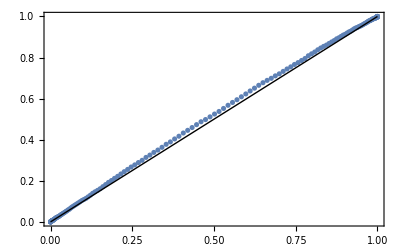

```mathematica
ProbabilityPlot[%429,numberOfRunsDistribution[10000]]
```

### Implementing 2

## ✓ Differences tests

### Brainstorming — First Order

#### Random Reals

```mathematica
sequence=RandomReal[{0,1},100000];
```

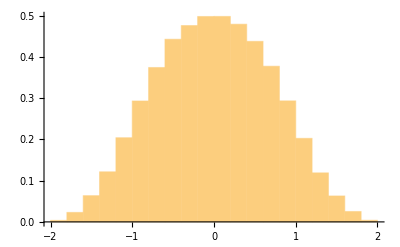

```mathematica
Histogram[Differences[sequence,2],Automatic,"PDF"]
```

```mathematica
TransformedDistribution[X-n,X\[Distributed]UniformSumDistribution[n]]
```

UniformSumDistribution[n,{-1,0}]

```mathematica
TransformedDistribution[X-3,X\[Distributed]UniformSumDistribution[3]]
```

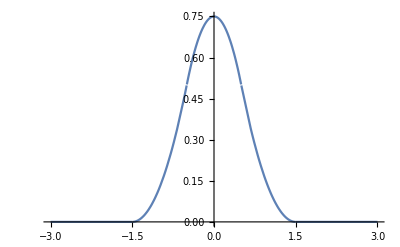

```mathematica
Plot[PDF[TransformedDistribution[X-3/2,X\[Distributed]UniformSumDistribution[3]],x],{x,-3,3}]
```

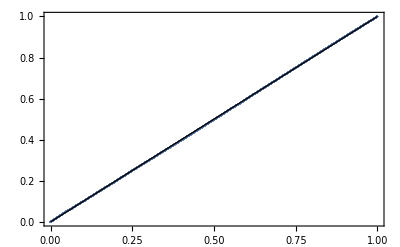

```mathematica
ProbabilityPlot[Differences[sequence,1],TransformedDistribution[X-2/2,X\[Distributed]UniformSumDistribution[2]]]
```

```mathematica
sequence=RandomReal[{0,1},1000];
```

```mathematica
KolmogorovSmirnovTest[Differences[sequence,1],TransformedDistribution[X-1,X\[Distributed]UniformSumDistribution[2]]]
```

0.606071

#### Random 0s and 1s

```mathematica
sequence=RandomInteger[{0,1},1000];
```

```mathematica
ArrayPlot[{sequence},ImageSize->Full]
```

-Graphics-

```mathematica
Histogram[Differences[sequence],Automatic,"PDF"]
```

### Brainstorming — nth Order

Consider a random sequence

{x_1,x_2,x_3,x_4,x_5,⋯,x_(n-2),x_(n-1),x_n}

## ✓ Overlapping permutations (OPERM5)

### Brainstorm

```mathematica
sequence=RandomInteger[{0,1},100];
```

```mathematica
Tuples[{0,1},5]
```

{{0,0,0,0,0},{0,0,0,0,1},{0,0,0,1,0},{0,0,0,1,1},{0,0,1,0,0},{0,0,1,0,1},{0,0,1,1,0},{0,0,1,1,1},{0,1,0,0,0},{0,1,0,0,1},{0,1,0,1,0},{0,1,0,1,1},{0,1,1,0,0},{0,1,1,0,1},{0,1,1,1,0},{0,1,1,1,1},{1,0,0,0,0},{1,0,0,0,1},{1,0,0,1,0},{1,0,0,1,1},{1,0,1,0,0},{1,0,1,0,1},{1,0,1,1,0},{1,0,1,1,1},{1,1,0,0,0},{1,1,0,0,1},{1,1,0,1,0},{1,1,0,1,1},{1,1,1,0,0},{1,1,1,0,1},{1,1,1,1,0},{1,1,1,1,1}}

```mathematica
$cts=Values@KeySort@(CountsBy[Tuples[{0,1},5],Total]/(N@Length[Tuples[{0,1},5]]))
```

{0.03125,0.15625,0.3125,0.3125,0.15625,0.03125}

```mathematica
N@PadRight[Values@KeySort@(Counts[Total/@Subsequences[RandomInteger[{0,1},500],{5}]]/Length[Subsequences[RandomInteger[{0,1},500],{5}]]),6]
```

{0.00604839,0.163306,0.318548,0.284274,0.183468,0.0443548}

```mathematica
Length[Subsequences[RandomInteger[{0,1},1000],{5}]]
```

996

```mathematica
OPERM5stat=Total[(PadRight[Values@KeySort@(Counts[Total/@Subsequences[#,{5}]]/(Length[#]-4)),6]-$cts)^2/$cts]&;
```

```mathematica
FindDistributionParameters[Table[stat[RandomInteger[{0,1},100]]]
```

0.919444

```mathematica
stat/@RandomInteger[{0,1},{10^4,100}];
```

```mathematica
Parallelize@Table[{n,β}/.FindDistributionParameters[stat/@RandomInteger[{0,1},{10^4,n}],GammaDistribution[α,β]],{n,1000,5000,500}]
```

{{1000,0.00590491},{1500,0.00399195},{2000,0.00304273},{2500,0.00240713},{3000,0.00200832},{3500,0.00173703},{4000,0.00153407},{4500,0.0013323},{5000,0.00119603}}

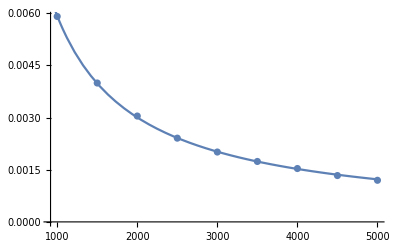

```mathematica
Show[ListPlot[%499],Plot[%509[x],{x,0,5000}]]
```

```mathematica
OPERM5αvsn=Table[{n,α}/.FindDistributionParameters[OPERM5stat/@RandomInteger[{0,1},{10^4,n}],GammaDistribution[α,β]],{n,1000,5000,500}]
```

{{1000,2.08948},{1500,2.02069},{2000,2.02426},{2500,2.09891},{3000,2.05497},{3500,2.0243},{4000,2.09671},{4500,2.03829},{5000,2.06398}}

```mathematica
αOPERM5=Mean[OPERM5αvsnᵀ⟦2⟧]
```

2.05684

```mathematica
βOPERM5[seqleng_]=%509[seqleng]
```

%509[seqleng]

```mathematica
NonlinearModelFit[%499,a x^b,{a,b},x]
```

FittedModel[5.15409/x^0.979917]

```mathematica
Table[OPERM5stat[RandomInteger[{0,1},10000]],1000];
```

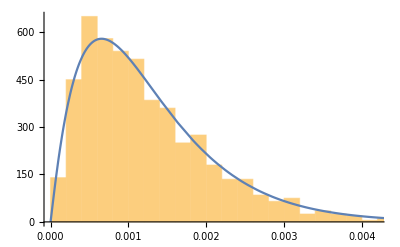

```mathematica
Show[Histogram[%,Automatic,"PDF"],Plot[PDF[OPERM5dist[10000],x],{x,0,.01},PlotRange->All]]
```

```mathematica
DistributionFitTest[%556,OPERM5dist[10000]]
```

0.943092

```mathematica
FindDistribution[%430,TargetFunctions->{GammaDistribution}]
```

GammaDistribution[2.03343,0.0120271]

```mathematica
OPERM5dist[seqleng_]=GammaDistribution[αOPERM5,βOPERM5[seqleng]]
```

GammaDistribution[2.05647,5.15409/seqleng^0.979917]

```mathematica
OPERM5stat[RandomInteger[{0,1},100000]]
```

0.0000430466

The test displays expected type I error!

```mathematica
Table[1-CDF[OPERM5dist[1000],OPERM5stat[RandomInteger[{0,1},1000]]],10000];
```

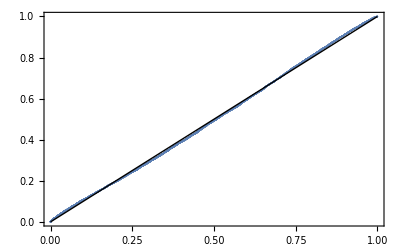

```mathematica
ProbabilityPlot[%,UniformDistribution[]]
```

```mathematica
1-CDF[OPERM5dist[Length[rule30seq]],OPERM5stat[rule30seq]]
```

0.764675

Rule 30 seems to be random!

## ✓ Autocorrelation

```mathematica
AutocorrelationTest[Take[N@rule30seq,1000],Automatic,{"TestDataTable",All}]
```

| Statistic | P-Value
Box-Pierce | 11.6261 | 0.113546
Ljung-Box | 11.6915 | 0.11117

## Gap tests

Only on random reals
Page 62 ★

### Brainstorming

```mathematica
sequence=RandomReal[{0,1},1000];
```

## Spectral Tests

## Overlapping sums (OSUMn)

### Brainstorming

```mathematica
sequence=RandomReal[{0,1},100000];
```

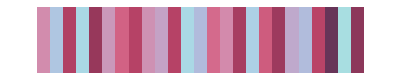

```mathematica
ArrayPlot[{RandomSample[sequence,25]},ColorFunction->"CandyColors",AspectRatio->Automatic,ImageSize->Full]
```

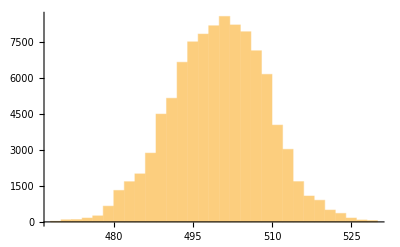

```mathematica
Histogram[Total/@Subsequences[sequence,{1000}]]
```

```mathematica
UniformSumDistribution[100]
```

UniformSumDistribution[100,{0,1}]

```mathematica
FindDistributionParameters[Total/@Subsequences[sequence,{1000}],NormalDistribution[μ,σ]]
```

{μ→499.736,σ→8.63983}

```mathematica
GammaDistribution[α,β]/.FindDistributionParameters[Total/@Subsequences[RandomReal[{0,1},100000],{1000}],GammaDistribution[α,β]]
```

GammaDistribution[3225.7,0.154501]

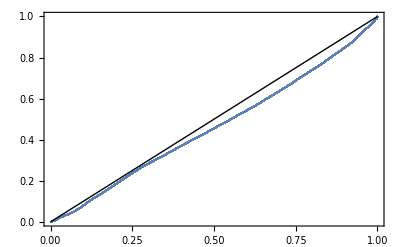

```mathematica
ProbabilityPlot[Total/@Subsequences[RandomReal[{0,1},100000],{1000}],GammaDistribution[3225.6994588174252,0.1545010290874235]]
```

```mathematica
LocationTest[Total/@Subsequences[sequence,{100}],50]
```

0.260026

```mathematica
Total/@Subsequences[sequence,{100}]
```

{45.2962,45.5133,45.5919,45.1799,44.6169,44.5231,99889,51.2486,51.3479,52.2374,52.1626,51.9738,52.9498}
 |  |  |  |

```mathematica
DistributionFitTest[Total/@Subsequences[RandomReal[{0,1},10000],{5}]]
```

0.00606352

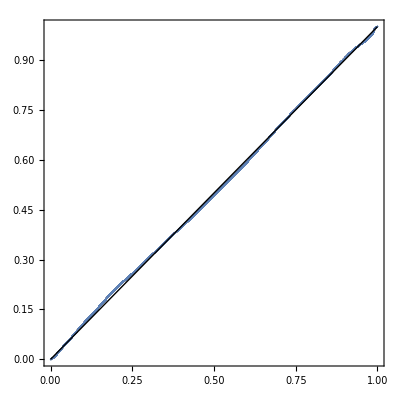

```mathematica
ProbabilityPlot[Total/@Subsequences[RandomReal[{0,1},100000],{1000}],AspectRatio->1]
```

```mathematica
OSUMnstatχ[seq_,n_]:=Total[(Mean/@Subsequences[seq,{n}]-1/2)^2/(1/2)]
```

```mathematica
Total/@Subsequences[sequence,{1000}]
```

{508.647,508.662,508.429,509.252,509.795,510.408,510.823,510.645,511.177,511.124,511.2,510.883,511.113,98975,502.805,503.203,502.821,503.207,502.791,501.948,501.953,502.789,503.213,503.146,502.98,503.252,503.062}
 |  |  |  |

```mathematica
OSUMnstatχ[Random,10]
```

1653.49

```mathematica
OSUMnstatmean[seq_,n_]:=Mean[Mean/@Subsequences[seq,{n}]]
```

```mathematica
sequence
```

```mathematica
Total[(Total/@Subsequences[sequence,{100}]-.5 100)^2/(.5  100)]
```

17536.7

```mathematica
Table[Total[(Mean/@Subsequences[RandomReal[{0,1},1000],{100}]-.5)^2/(.5)],1000]
```

```mathematica
GammaDistribution[α,β]/.FindDistributionParameters[%609,GammaDistribution[α,β]]
```

GammaDistribution[7.62933,0.194779]

```mathematica
DistributionFitTest[%609,GammaDistribution[7.629327599137594,0.19477924125305393]]
```

0.551077

```mathematica
Length[Total/@Subsequences[sequence,{100}]]
```

99901

```mathematica
DiscretePlot[OSUMnstatmean[sequence,n],{n,5,50000,10000}]
```

$Aborted[]

```mathematica
OSUMnstatmean[sequence,1000]/1000
```

0.49987

```mathematica
1/2 n
```

```mathematica
OSUMnstatmean[#,10]&/@RandomReal[{0,1},{10000,1000}];
```

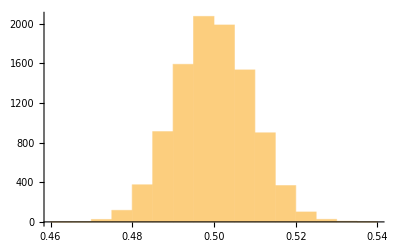

```mathematica
Histogram[%161]
```

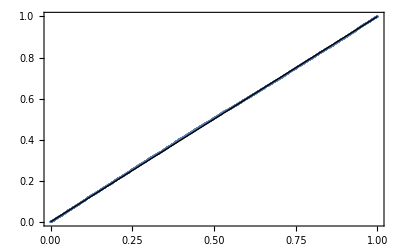

```mathematica
ProbabilityPlot[%161]
```

```mathematica
KolmogorovSmirnovTest[%31]
```

0.844567

```mathematica
Table[{seqleng,StandardDeviation[OSUMnstatmean[#,100]&/@RandomReal[{0,1},{1000,seqleng}]]},{seqleng,1000,10000,1000}]
```

{{1000,0.00926192},{2000,0.00660548},{3000,0.00523465},{4000,0.00448585},{5000,0.00406819},{6000,0.00379244},{7000,0.00345482},{8000,0.0032889},{9000,0.00307945},{10000,0.00287389}}

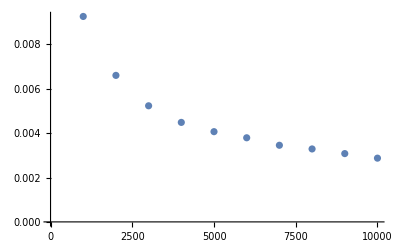

```mathematica
ListPlot[%37]
```

```mathematica
NonlinearModelFit[%37,a x^b,{a,b},x]
```

FittedModel[0.306693/x^0.506635]

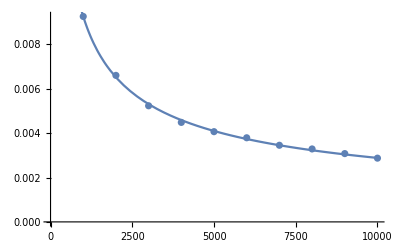

```mathematica
Show[ListPlot[%37],Plot[%41[x],{x,0,10000}]]
```

```mathematica
NormalDistribution[.5,%41[10000]]
```

```mathematica
OSUMnstatmean[#,100]&/@RandomReal[{0,1},{10000,10000}];
```

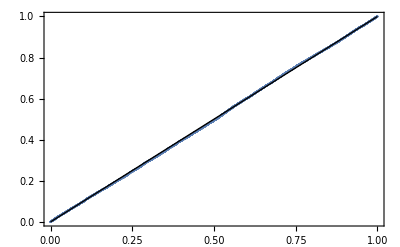

```mathematica
ProbabilityPlot[%48,NormalDistribution[.5,%41[10000]]]
```

## Maximum test

### Brainstorming

```mathematica
sequence=RandomReal[{0,1},1000];
```

```mathematica
Mean@TakeLargest[sequence,50]
```

0.979701

```mathematica
Table[Times[##/.List->Sequence]&@TakeLargest[RandomReal[{0,1},1000],50],10000];
```

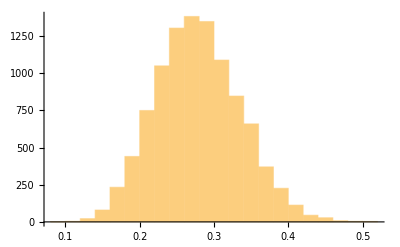

```mathematica
Histogram[%]
```

```mathematica
CDF[BetaDistribution[1000,1],Max[sequence]]
```

0.862772

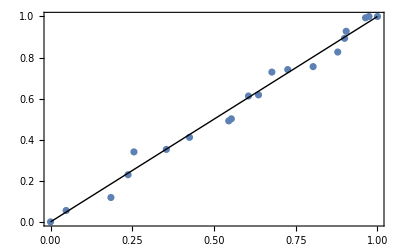

```mathematica
ProbabilityPlot[%90,BetaDistribution[1,100]]
```

```mathematica
DistributionFitTest[%90,BetaDistribution[1,1000]]
```

2.33846×10^-8

```mathematica
N@StandardDeviation[TransformedDistribution[X+ Y+Z,{X\[Distributed]BetaDistribution[1,1000],Y\[Distributed]BetaDistribution[999,2],Z\[Distributed]BetaDistribution[998,3]}]]
```

0.00244297

```mathematica
OrderDistribution[{UniformDistribution[],1000},{1000,999}]
```

OrderDistribution[{UniformDistribution[{0,1}],1000},{1000,999}]

```mathematica
PDF[BetaDistribution[100,1],x]
```

Piecewise[{{100 x^99, 0<x<1}, {0, True}}]